# Infection by SARS-CoV-2 with alternate frequencies of mRNA vaccine boosting for patients undergoing antineoplastic treatment for cancer

Jeffrey P. Townsend, Hayley B. Hassler, Brinda Emu, Alex Dornburg

## SARS-CoV-2 (Gudbjartsson)

Input Data: Average peak-normalized ELIZA ODs for SARS-CoV-2 S1 IgG antibodies from Gudbjartsson et al. 2020, “Humoral Immune Response to SARS-CoV-2 in Iceland”, New England Journal of Medicine. scaled to post-BNT162b2 (Pfizer-BioNTech) booster vaccination level using the average peak value from 110 naive individuals from Kontopoulou et al. 2022 “Significant Increase in Antibody Titers after the 3rd Booster Dose of the Pfizer–BioNTech mRNA COVID-19 Vaccine in Healthcare Workers in Greece”, Vaccines.

days : 34, 48, 70, 94, 109
OD : 1.6, 1.55, 1.43, 1.19, 1.22

```mathematica
sarscov2data={
{1,34, SARSCoV2,1.6/1.6,  TRUE,NA, NA},
{2,48, SARSCoV2,1.55/1.6, FALSE, (48-34), (1.55/1.6-1.6/1.6)/(48-34)},
{3, 70, SARSCoV2,1.43/1.6,  FALSE,(70-48), (1.43/1.6-1.55/1.6)/(70-48)},
{4, 94, SARSCoV2,1.19/1.6, FALSE,(94-70),  (1.19/1.6-1.43/1.6)/(94-70)}
}
```

{{1,34,SARSCoV2,1.,TRUE,NA,NA},{2,48,SARSCoV2,0.96875,FALSE,14,-0.00223214},{3,70,SARSCoV2,0.89375,FALSE,22,-0.00340909},{4,94,SARSCoV2,0.74375,FALSE,24,-0.00625}}

### SARS-CoV-2 Waning of Antibody OD

```mathematica
sarscov2datalength=Length[sarscov2data]
```

4

```mathematica
Table[
{aod,
Table[
If [
Or[
sarscov2data[[index-1, 4]]≥aod≥sarscov2data[[index, 4]],
sarscov2data[[index-1, 4]]≤aod≤sarscov2data[[index, 4]]],
sarscov2data[[index, 7]],
Nothing],
{index, 2, sarscov2datalength}
]
}
, {aod,  0.75,1, 0.05}]
```

{{0.75,{-0.00625}},{0.8,{-0.00625}},{0.85,{-0.00625}},{0.9,{-0.00340909}},{0.95,{-0.00340909}},{1.,{-0.00223214}}}

```mathematica
sarscov2paddedmeanwaning=Table[
{aod,
Table[
If [
Or[
sarscov2data[[index-1, 4]]≥aod≥sarscov2data[[index, 4]],
sarscov2data[[index-1, 4]]≤aod≤sarscov2data[[index, 4]]],
sarscov2data[[index, 7]],
Nothing],
{index, 2, sarscov2datalength}
]
}
, {aod, 0.75,1.25, 0.05}]
```

{{0.75,{-0.00625}},{0.8,{-0.00625}},{0.85,{-0.00625}},{0.9,{-0.00340909}},{0.95,{-0.00340909}},{1.,{-0.00223214}},{1.05,{}},{1.1,{}},{1.15,{}},{1.2,{}},{1.25,{}}}

Mean waning extended to rituximab BNT162b2-scaled peak (1.500037185) from Peeters et al. 2021.

```mathematica
sarscov2meanwaningTLM={{0.75,{-0.00625}},{0.8,{-0.00625}},{0.85,{-0.00625}},{0.9,{-0.0034090909090909124}},{0.95,{-0.0034090909090909124}},{1.,{-0.002232142857142857}}}
```

{{0.75,{-0.00625}},{0.8,{-0.00625}},{0.85,{-0.00625}},{0.9,{-0.00340909}},{0.95,{-0.00340909}},{1.,{-0.00223214}}}

```mathematica
TableForm[sarscov2meanwaningTLM]
```

0.75 | -0.00625
0.8 | -0.00625
0.85 | -0.00625
0.9 | -0.00340909
0.95 | -0.00340909
1. | -0.00223214

```mathematica
sarscov2antibodywaningTLM=Interpolation[sarscov2meanwaningTLM]
```

InterpolatingFunction[…]

```mathematica
sarscov2antibodytimecourseTLM={1};
day=1;
While[sarscov2antibodytimecourseTLM[[day]]≥0.75,
sarscov2antibodytimecourseTLM=Append[sarscov2antibodytimecourseTLM, sarscov2antibodytimecourseTLM[[day]]+sarscov2antibodywaningTLM[sarscov2antibodytimecourseTLM[[day]]]];
sarscov2antibodytimecourseTLM=Flatten[sarscov2antibodytimecourseTLM];
Increment[day];
];
sarscov2antibodytimecourseTLM
```

{1,0.997768,0.995402,0.992906,0.990284,0.987541,0.984687,0.981728,0.978675,0.97554,0.972332,0.969064,0.965746,0.962391,0.959008,0.955607,0.952197,0.948786,0.945379,0.941982,0.938598,0.935231,0.931879,0.928545,0.925226,0.921921,0.918624,0.915332,0.912039,0.908738,0.90542,0.902076,0.898696,0.895224,0.891577,0.887733,0.883672,0.879371,0.87481,0.869969,0.864831,0.859383,0.853621,0.84755,0.841257,0.834882,0.828462,0.82203,0.815612,0.809229,0.802894,0.796617,0.790399,0.784236,0.778121,0.772038,0.76597,0.759893,0.753779,0.747592}

```mathematica
sarscov2baseline=0.1641335
```

0.164134

This baseline peak-normalized S IgG antibody level for SARS-CoV-2 comes from the ancestral and descendent states analysis that used the baselines for the human “seasonal” coronaviruses to estimate the baselines for the zoonotic coronaviruses. See Townsend et al. 2021 “The durability of immunity against reinfection by SARS-CoV-2: a comparative evolutionary study”, The Lancet Microbe.

```mathematica
scalarsabove1=Table[(1.422592491177772-0.422592491177772*(index-1)/(Length[sarscov2antibodytimecourseTLM]-1))/1.422592491177772, {index, Length[sarscov2antibodytimecourseTLM]}]
```

{1.,0.994965,0.98993,0.984895,0.97986,0.974826,0.969791,0.964756,0.959721,0.954686,0.949651,0.944616,0.939581,0.934547,0.929512,0.924477,0.919442,0.914407,0.909372,0.904337,0.899302,0.894267,0.889233,0.884198,0.879163,0.874128,0.869093,0.864058,0.859023,0.853988,0.848954,0.843919,0.838884,0.833849,0.828814,0.823779,0.818744,0.813709,0.808675,0.80364,0.798605,0.79357,0.788535,0.7835,0.778465,0.77343,0.768395,0.763361,0.758326,0.753291,0.748256,0.743221,0.738186,0.733151,0.728116,0.723082,0.718047,0.713012,0.707977,0.702942}

```mathematica
sarscov2antibodytimecourseBPtoExp=(sarscov2antibodytimecourseTLM+0.500037185)*scalarsabove1
```

{1.50004,1.49026,1.48038,1.47039,1.46031,1.45013,1.43987,1.42954,1.41915,1.40871,1.39824,1.38774,1.37722,1.36671,1.3562,1.34571,1.33525,1.32481,1.31442,1.30407,1.29377,1.28351,1.27331,1.26315,1.25304,1.24297,1.23295,1.22296,1.21301,1.20308,1.19317,1.18327,1.17337,1.16344,1.15339,1.14322,1.1329,1.12244,1.1118,1.10099,1.08999,1.07879,1.06741,1.05583,1.04415,1.03247,1.02081,1.00921,0.997691,0.986258,0.974926,0.963701,0.952582,0.941567,0.930648,0.919814,0.909052,0.898345,0.887673,0.877011}

```mathematica
Export["/Users/jt436/Downloads/alshukairi-gudbjartsson-SARS-CoV-2-Antibody-Time-Course_Pfizer_BoosterPeaktoExp.csv", sarscov2antibodytimecourseTLM]
```

Export::nodir: Directory /Users/jt436/Downloads/ does not exist.

OpenWrite::noopen: Cannot open /Users/jt436/Downloads/alshukairi-gudbjartsson-SARS-CoV-2-Antibody-Time-Course_Pfizer_BoosterPeaktoExp.csv.

$Failed

Used natural infection lambda value imputed in Townsend et al. 2021 “The durability of immunity against reinfection by SARS-CoV-2: a comparative evolutionary study”, The Lancet Microbe.

```mathematica
sarscov2halflife=Log[2]/ lambda /.lambda->0.0044587480795691795
```

155.458

```mathematica
Length[sarscov2antibodytimecourseBPtoExp]
```

60

```mathematica
sarscov2antibodytimecourseB=sarscov2antibodytimecourseBPtoExp;
day=Length[sarscov2antibodytimecourseB];
While[day<4393,
Increment[day];
AppendTo[sarscov2antibodytimecourseB, sarscov2baseline+(sarscov2antibodytimecourseB[[day-1]]- sarscov2baseline)*Exp[-lambda /.lambda->0.0044587480795691795]]
]
```

```mathematica
sarscov2antibodytimecourseB = {0.4499261566934753,0.44865471585787925,0.447388931437032,0.44612877826654773,0.4448742312939924,0.44362526557838583,0.4423818562897059,0.4411439787083947,0.4399116082248675,0.4386847203390231,0.43746329065975686,0.43624729490447595,0.43503670889861634,0.4338315085751625,0.43263166997416874,0.43143716924228287,0.4302479826322721,0.4290640865025508,0.42788545731671057,0.42671207164305236,0.4255439061541206,0.4243809376262393,0.42322314293905067,0.42207049907505517,0.4209229831191541,0.41978057225819393,0.4186432437805128,0.41751097507548907,0.4163837436330916,0.41526152704343255,0.4141443029963216,0.4130320492808225,0.4119247437848116,0.410822364494538,0.4097248894941864,0.4086322969654407,0.4075445651870508,0.4064616725344006,0.40538359747907804,0.4043103185884472,0.403241814525222,0.40217806404704237,0.40111904600605164,0.4000647393484762,0.39901512311420684,0.39797017643638233,0.3969298785409744,0.3958942087463746,0.39486314646298337,0.39383667119280064,0.3928147625290183,0.3917974001556145,0.39078456384694976,0.3897762334673649,0.3887723889707807,0.38777301040029943,0.386778077887808,0.385787571653583,0.38480147200589765,0.38381975934063006,0.3828424141408736,0.3818694169765489,0.3809007485040176,0.37993638946569774,0.3789763206896809,0.37802052308935113,0.3770689776630054,0.3761216654934759,0.37517856774775404,0.3742396656766157,0.373304940614249,0.3723743739778828,0.3714479472674175,0.370525642065057,0.36960744003494295,0.3686933229227897,0.36778327255552196,0.36687727084091304,0.3659752997672254,0.36507734140285253,0.3641833778959625,0.36329339147414297,0.36240736444404786,0.3615252791910458,0.3606471181788697,0.3597728639492681,0.3589024991216584,0.358036006392781,0.3571733685363555,0.3563145684027382,0.3554595889185809,0.35460841308649205,0.35376102398469816,0.3529174047667079,0.3520775386609769,0.3512414089705745,0.3504089990728516,0.3495802924191104,0.3487552725342754,0.34793392301656556,0.34711622753716864,0.34630216983991635,0.3454917337409612,0.3446849031284548,0.34388166196222747,0.3430819942734694,0.3422858841644132,0.3414933158080178,0.34070427344765386,0.33991874139679046,0.33913670403868335,0.33835814582606427,0.3375830512808321,0.33681140499374507,0.33604319162411433,0.33527839589949904,0.33451700261540274,0.3337589966349711,0.33300436288869095,0.3322530863740907,0.3315051521554421,0.33076054536346333,0.3300192511950234,0.32928125491284777,0.32854654184522547,0.32781509738571724,0.3270869069928654,0.3263619561899046,0.3256402305644741,0.3249217157683311,0.3242063975170657,0.32349426158981665,0.3227852938289889,0.3220794801399721,0.3213768064908602,0.3206772589121726,0.31998082349657647,0.3192874863986103,0.3185972338344085,0.3179100520814276,0.317225927478173,0.316544846423928,0.31586679537848283,0.31519176086186584,0.31451972945407536,0.3138506877948129,0.31318462258321755,0.3125215205776017,0.3118613685951874,0.31120415351184494,0.3105498622618311,0.3098984818375301,0.3092499992891946,0.30860440172468856,0.3079616763092306,0.30732181026513905,0.30668479087157796,0.306050605464304,0.30541924143541493,0.30479068623309874,0.30416492736138423,0.30354195237989257,0.30292174890359,0.30230430460254154,0.3016896072016659,0.3010776444804914,0.3004684042729132,0.29986187446695123,0.2992580430045094,0.29865689788113614,0.29805842714578534,0.2974626189005791,0.296869461300571,0.29627894255351084,0.2956910509196098,0.2951057747113075,0.29452310229303935,0.2939430220810054,0.2933655225429399,0.2927905921978821,0.29221821961594807,0.29164839341810334,0.29108110227593675,0.29051633491143536,0.28995408009675994,0.289394326654022,0.28883706345506144,0.2882822794212255,0.28772996352314817,0.28718010478053135,0.2866326922619263,0.2860877150845162,0.2855451624139001,0.28500502346387735,0.2844672874962331,0.2839319438205251,0.2833989817938708,0.282868390820736,0.28234016035272425,0.28181427988836694,0.28129073897291457,0.28076952719812914,0.28025063420207696,0.27973404966892274,0.2792197633287245,0.2787077649572295,0.27819804437567075,0.27769059145056485,0.27718539609351056,0.276682448260988,0.2761817379541592,0.27568325521866927,0.2751869901444484,0.27469293286551505,0.2742010735597796,0.27371140244884906,0.273223909797833,0.27273858591514966,0.27225542115233337,0.2717744059038429,0.2712955306068702,0.2708187857411507,0.2703441618287735,0.2698716494339935,0.26940123916304337,0.2689329216639471,0.26846668762633397,0.26800252778125333,0.2675404329009906,0.26708039379888354,0.26662240132913984,0.2661664463866551,0.265712519906832,0.26526061286539987,0.2648107162782356,0.2643628212011848,0.263916918729884,0.26347299999958357,0.26303105618497175,0.26259107849999896,0.2621530581977032,0.26171698657003606,0.2612828549476898,0.26085065469992497,0.2604203772343985,0.25999201399699334,0.25956555647164814,0.25914099618018793,0.2587183246821558,0.2582975335746447,0.2578786144921308,0.25746155910630697,0.25704635912591717,0.25663300629659175,0.2562214924006833,0.25581180925710323,0.2554039487211591,0.254997902684393,0.2545936630744198,0.2541912218547671,0.2537905710247155,0.2533917026191391,0.2529946087083477,0.25259928139792875,0.2522057128285905,0.25181389517600583,0.2514238206506567,0.2510354814976793,0.25064886999670966,0.25026397846173054,0.24988079924091827,0.24949932471649092,0.2491195473045566,0.2487414594549629,0.24836505365114664,0.24799032240998453,0.24761725828164433,0.24724585384943681,0.24687610172966834,0.24650799457149392,0.24614152505677117,0.24577668589991492,0.24541346984775214,0.24505186967937803,0.2446918782060122,0.24433348827085594,0.24397669274894979,0.24362148454703206,0.24326785660339767,0.24291580188775783,0.2425653134011002,0.24221638417554997,0.24186900727423094,0.24152317579112803,0.24117888285094968,0.24083612160899134,0.24049488525099932,0.24015516699303535,0.23981696008134168,0.23948025779220683,0.23914505343183196,0.23881134033619766,0.23847911187093168,0.23814836143117682,0.23781908244145977,0.2374912683555603,0.2371649126563812,0.23684000885581863,0.23651655049463316,0.23619453114232142,0.23587394439698817,0.23555478388521908,0.23523704326195402,0.23492071621036087,0.23460579644171003,0.2342922776952493,0.23398015373807945,0.23366941836503038,0.23336006539853765,0.23305208868851965,0.2327454821122555,0.23244023957426307,0.23213635500617813,0.2318338223666334,0.23153263564113868,0.23123278884196102,0.23093427600800592,0.23063709120469877,0.23034122852386674,0.23004668208362147,0.22975344602824208,0.2294615145280587,0.22917088177933673,0.22888154200416122,0.22859348945032226,0.22830671839120042,0.22802122312565304,0.2277369979779008,0.22745403729741492,0.22717233545880483,0.2268918868617063,0.2266126859306702,0.22633472711505145,0.22605800488889893,0.22578251375084546,0.22550824822399845,0.22523520285583104,0.22496337221807367,0.22469275090660623,0.22442333354135058,0.2241551147661636,0.22388808924873063,0.22362225168045963,0.22335759677637546,0.22309411927501496,0.22283181393832224,0.22257067555154464,0.22231069892312896,0.22205187888461833,0.2217942102905494,0.22153768801835014,0.22128230696823784,0.22102806206311787,0.2207749482484827,0.2205229604923114,0.22027209378496962,0.22002234313910995,0.21977370358957282,0.2195261701932878,0.21927973802917525,0.2190344021980486,0.21879015782251682,0.2185470000468876,0.21830492403707072,0.21806392498048197,0.21782399808594746,0.2175851385836084,0.21734734172482623,0.21711060278208827,0.21687491704891368,0.21664027983975995,0.21640668648992967,0.2161741323554779,0.21594261281311974,0.2157121232601385,0.21548265911429412,0.21525421581373216,0.21502678881689302,0.2148003736024217,0.21457496566907794,0.21435056053564666,0.21412715374084892,0.21390474084325323,0.21368331742118724,0.21346287907264982,0.21324342141522362,0.2130249400859878,0.21280743074143144,0.2125908890573671,0.21237531072884488,0.2121606914700669,0.21194702701430193,0.21173431311380078,0.21152254553971167,0.21131172008199625,0.2111018325493459,0.21089287876909835,0.2106848545871548,0.2104777558678973,0.2102715784941065,0.21006631836687986,0.20986197140555013,0.2096585335476042,0.20945600074860235,0.2092543689820979,0.20905363423955708,0.20885379253027941,0.2086548398813183,0.20845677233740212,0.2082595859608555,0.20806327683152115,0.2078678410466818,0.20767327472098268,0.20747957398635436,0.20728673499193567,0.2070947539039973,0.20690362690586545,0.2067133501978461,0.20652391999714934,0.20633533253781428,0.20614758407063405,0.2059606708630814,0.20577458919923441,0.20558933537970264,0.20540490572155354,0.20522129655823934,0.20503850423952402,0.2048565251314109,0.20467535561607023,0.20449499209176736,0.20431543097279117,0.20413666868938268,0.20395870168766414,0.20378152642956837,0.20360513939276842,0.2034295370706076,0.20325471597202965,0.20308067262150942,0.20290740355898376,0.20273490533978272,0.2025631745345611,0.20239220772923022,0.2022220015248901,0.20205255253776183,0.20188385739912035,0.20171591275522746,0.20154871526726514,0.2013822616112692,0.2012165484780632,0.20105157257319253,0.20088733061685915,0.20072381934385616,0.20056103550350307,0.20039897585958102,0.20023763719026857,0.20007701628807756,0.1999171099597894,0.19975791502639154,0.19959942832301428,0.1994416466988679,0.19928456701718,0.19912818615513306,0.19897250100380243,0.19881750846809457,0.19866320546668542,0.19850958893195922,0.19835665580994744,0.19820440306026815,0.19805282765606552,0.19790192658394967,0.19775169684393676,0.19760213544938934,0.197453239426957,0.19730500581651722,0.19715743167111655,0.19701051405691197,0.1968642500531127,0.19671863675192194,0.19657367125847924,0.1964293506908028,0.1962856721797323,0.1961426328688718,0.19600022991453292,0.1958584604856784,0.19571732176386575,0.19557681094319118,0.19543692523023393,0.19529766184400063,0.19515901801587007,0.19502099098953815,0.1948835780209631,0.19474677637831084,0.19461058334190082,0.1944749962041518,0.1943400122695281,0.19420562885448606,0.19407184328742053,0.19393865290861192,0.1938060550701733,0.1936740471359976,0.19354262648170542,0.19341179049459273,0.19328153657357897,0.19315186212915528,0.19302276458333312,0.19289424136959293,0.19276628993283318,0.1926389077293195,0.19251209222663412,0.1923858409036256,0.1922601512503586,0.19213502076806413,0.19201044696908967,0.1918864273768499,0.19176295952577738,0.19164004096127346,0.19151766923965968,0.191395841928129,0.19127455660469755,0.1911538108581564,0.19103360228802366,0.1909139285044968,0.19079478712840503,0.19067617579116217,0.19055809213471936,0.19044053381151832,0.19032349848444466,0.19020698382678136,0.1900909875221626,0.1899755072645276,0.1898605407580749,0.18974608571721657,0.18963213986653293,0.18951870094072723,0.1894057666845806,0.18929333485290722,0.18918140321050975,0.1890699695321348,0.1889590316024288,0.18884858721589384,0.1887386341768439,0.18862917029936116,0.1885201934072526,0.18841170133400664,0.1883036919227502,0.18819616302620568,0.18808911250664834,0.18798253823586386,0.1878764380951059,0.18777080997505408,0.187665651775772,0.1875609614066655,0.18745673678644115,0.18735297584306476,0.1872496765137203,0.1871468367447688,0.18704445449170762,0.18694252771912967,0.1868410544006831,0.18674003251903093,0.18663946006581092,0.1865393350415957,0.186439655455853,0.18634041932690606,0.18624162468189426,0.18614326955673385,0.18604535199607902,0.1859478700532829,0.18585082179035886,0.18575420527794212,0.18565801859525122,0.18556225983004998,0.1854669270786094,0.1853720184456698,0.18527753204440323,0.18518346599637583,0.18508981843151062,0.18499658748805026,0.18490377131252,0.1848113680596909,0.18471937589254311,0.18462779298222934,0.18453661750803854,0.18444584765735966,0.18435548162564566,0.1842655176163776,0.18417595384102892,0.18408678851902988,0.18399801987773223,0.1839096461523739,0.1838216655860439,0.18373407642964748,0.18364687694187126,0.18356006538914868,0.1834736400456255,0.18338759919312547,0.18330194112111625,0.18321666412667534,0.1831317665144562,0.18304724659665467,0.18296310269297525,0.18287933313059782,0.1827959362441443,0.18271291037564566,0.1826302538745088,0.18254796509748383,0.18246604240863143,0.18238448417929026,0.18230328878804458,0.1822224546206921,0.18214198007021173,0.18206186353673187,0.18198210342749835,0.1819026981568429,0.18182364614615168,0.18174494582383374,0.1816665956252899,0.18158859399288158,0.18151093937589988,0.18143363023053471,0.18135666501984415,0.18128004221372382,0.18120376028887653,0.18112781772878195,0.1810522130236665,0.18097694467047332,0.18090201117283236,0.18082741104103067,0.18075314279198276,0.18067920494920114,0.18060559604276694,0.18053231460930066,0.18045935919193318,0.1803867283402767,0.18031442061039593,0.18024243456477945,0.180170768772311,0.18009942180824112,0.18002839225415884,0.17995767869796342,0.17988727973383628,0.17981719396221316,0.17974741998975613,0.17967795642932605,0.17960880189995482,0.1795399550268181,0.1794714144412079,0.1794031787805053,0.17933524668815348,0.17926761681363074,0.1792002878124235,0.1791332583459998,0.1790665270817825,0.1790000926931229,0.17893395385927424,0.17886810926536567,0.17880255760237584,0.17873729756710707,0.17867232786215936,0.1786076471959046,0.17854325428246093,0.17847914784166713,0.17841532659905718,0.17835178928583495,0.17828853463884897,0.1782255614005673,0.17816286831905254,0.1781004541479369,0.1780383176463975,0.17797645757913164,0.17791487271633227,0.17785356183366355,0.17779252371223647,0.17773175713858466,0.17767126090464022,0.17761103380770976,0.17755107465045042,0.17749138224084615,0.17743195539218393,0.17737279292303026,0.1773138936572076,0.177255256423771,0.17719688005698483,0.1771387633962997,0.17708090528632917,0.177023304576827,0.17696596012266416,0.17690887078380613,0.17685203542529013,0.1767954529172027,0.17673912213465712,0.1766830419577711,0.17662721127164452,0.17657162896633724,0.17651629393684706,0.17646120508308774,0.1764063613098671,0.1763517615268653,0.17629740464861313,0.17624328959447047,0.17618941528860474,0.17613578065996954,0.17608238464228343,0.17602922617400857,0.1759763041983298,0.1759236176631335,0.17587116552098672,0.17581894672911638,0.17576696024938848,0.1757152050482875,0.17566368009689584,0.17561238437087343,0.17556131685043722,0.17551047652034105,0.1754598623698554,0.1754094733927473,0.17535930858726032,0.1753093669560947,0.17525964750638748,0.17521014924969275,0.17516087120196203,0.1751118123835247,0.1750629718190685,0.1750143485376202,0.17496594157252626,0.17491774996143358,0.17486977274627039,0.17482200897322725,0.174774457692738,0.174727117959461,0.17467998883226019,0.17463306937418652,0.17458635865245922,0.17453985573844732,0.17449355970765115,0.174447469639684,0.17440158461825372,0.1743559037311447,0.17431042607019953,0.17426515073130106,0.17422007681435436,0.17417520342326895,0.1741305296659408,0.17408605465423477,0.17404177750396682,0.17399769733488651,0.17395381327065948,0.17391012443885,0.1738666299709037,0.17382332900213024,0.1737802206716861,0.17373730412255753,0.17369457850154346,0.1736520429592386,0.1736096966500165,0.1735675387320127,0.1735255683671081,0.17348378472091228,0.17344218696274674,0.17340077426562867,0.17335954580625426,0.1733185007649825,0.17327763832581877,0.17323695767639868,0.1731964580079719,0.1731561385153861,0.17311599839707092,0.17307603685502207,0.17303625309478537,0.17299664632544112,0.17295721575958822,0.1729179606133286,0.17287888010625158,0.1728399734614184,0.17280123990534685,0.17276267866799566,0.17272428898274944,0.1726860700864033,0.1726480212191477,0.17261014162455343,0.1725724305495564,0.17253488724444282,0.17249751096283425,0.17246030096167272,0.17242325650120605,0.17238637684497302,0.17234966125978884,0.17231310901573052,0.17227671938612235,0.1722404916475215,0.1722044250797036,0.17216851896564841,0.17213277259152562,0.17209718524668058,0.17206175622362024,0.1720264848179991,0.1719913703286051,0.1719564120573458,0.17192160930923442,0.17188696139237605,0.17185246761795392,0.17181812730021567,0.17178393975645975,0.1717499043070218,0.17171602027526117,0.17168228698754748,0.1716487037732472,0.17161526996471033,0.17158198489725712,0.17154884790916491,0.17151585834165486,0.17148301553887896,0.17145031884790693,0.1714177676187133,0.1713853612041644,0.17135309896000556,0.1713209802448483,0.17128900442015751,0.17125717085023892,0.17122547890222622,0.17119392794606872,0.17116251735451862,0.1711312465031187,0.17110011477018983,0.17106912153681858,0.17103826618684503,0.17100754810685037,0.17097696668614482,0.17094652131675545,0.17091621139341406,0.17088603631354524,0.17085599547725427,0.17082608828731533,0.17079631414915947,0.1707666724708629,0.17073716266313524,0.17070778413930768,0.17067853631532146,0.17064941860971616,0.1706204304436182,0.17059157124072924,0.1705628404273149,0.17053423743219315,0.17050576168672307,0.17047741262479355,0.17044918968281197,0.1704210922996931,0.17039311991684777,0.17036527197817197,0.17033754793003567,0.17030994722127182,0.17028246930316543,0.17025511362944265,0.1702278796562599,0.17020076684219307,0.17017377464822675,0.1701469025377435,0.1701201499765132,0.17009351643268242,0.17006700137676387,0.17004060428162585,0.17001432462248178,0.16998816187687973,0.16996211552469212,0.1699361850481053,0.1699103699316092,0.16988466966198734,0.1698590837283063,0.16983361162190574,0.1698082528363883,0.1697830068676095,0.16975787321366764,0.16973285137489394,0.16970794085384255,0.1696831411552807,0.16965845178617875,0.16963387225570054,0.16960940207519348,0.16958504075817898,0.16956078782034267,0.1695366427795248,0.16951260515571065,0.16948867447102103,0.1694648502497028,0.16944113201811922,0.16941751930474083,0.16939401164013582,0.16937060855696084,0.16934730958995164,0.1693241142759139,0.16930102215371393,0.1692780327642695,0.16925514565054087,0.16923236035752148,0.16920967643222906,0.1691870934236966,0.1691646108829633,0.16914222836306578,0.16911994541902906,0.16909776160785778,0.16907567648852742,0.1690536896219755,0.16903180057109285,0.16901000890071488,0.168988314177613,0.168966715970486,0.16894521384995137,0.16892380738853696,0.1689024961606723,0.1688812797426802,0.16886015771276836,0.16883912965102096,0.16881819513939034,0.16879735376168858,0.16877660510357936,0.16875594875256966,0.16873538429800158,0.16871491133104413,0.16869452944468516,0.16867423823372327,0.16865403729475967,0.16863392622619028,0.16861390462819764,0.16859397210274302,0.16857412825355853,0.16855437268613913,0.16853470500773493,0.1685151248273433,0.16849563175570106,0.1684762254052769,0.16845690539026345,0.1684376713265698,0.1684185228318138,0.16839945952531438,0.16838048102808412,0.16836158696282164,0.16834277695390407,0.16832405062737962,0.16830540761096022,0.16828684753401396,0.16826837002755785,0.1682499747242504,0.1682316612583844,0.1682134292658796,0.16819527838427542,0.1681772082527239,0.16815921851198234,0.16814130880440634,0.16812347877394251,0.1681057280661215,0.168088056328051,0.16807046320840852,0.16805294835743464,0.16803551142692597,0.16801815207022816,0.1680008699422291,0.167983664699352,0.16796653599954858,0.16794948350229227,0.1679325068685715,0.16791560576088282,0.16789877984322432,0.1678820287810889,0.1678653522414576,0.16784874989279303,0.16783222140503273,0.16781576644958265,0.16779938469931058,0.16778307582853966,0.16776683951304192,0.16775067543003183,0.16773458325815988,0.16771856267750612,0.16770261336957396,0.1676867350172837,0.16767092730496627,0.16765518991835696,0.16763952254458916,0.1676239248721882,0.167608396591065,0.1675929373925101,0.16757754696918742,0.16756222501512813,0.16754697122572465,0.1675317852977245,0.16751666692922434,0.16750161581966394,0.1674866316698202,0.1674717141818012,0.16745686305904034,0.16744207800629035,0.16742735872961745,0.16741270493639557,0.16739811633530044,0.16738359263630384,0.16736913355066785,0.1673547387909391,0.16734040807094303,0.16732614110577823,0.16731193761181076,0.16729779730666855,0.16728371990923568,0.16726970513964695,0.16725575271928217,0.16724186237076072,0.16722803381793597,0.1672142667858898,0.1672005610009272,0.16718691619057077,0.16717333208355528,0.16715980840982236,0.16714634490051505,0.1671329412879725,0.16711959730572457,0.16710631268848672,0.16709308717215451,0.16707992049379852,0.16706681239165905,0.16705376260514085,0.1670407708748081,0.16702783694237913,0.16701496055072132,0.16700214144384595,0.16698937936690322,0.16697667406617708,0.1669640252890802,0.16695143278414895,0.16693889630103848,0.16692641559051766,0.1669139904044641,0.16690162049585933,0.16688930561878373,0.16687704552841184,0.16686483998100732,0.16685268873391818,0.16684059154557193,0.16682854817547083,0.16681655838418705,0.16680462193335793,0.16679273858568128,0.16678090810491056,0.16676913025585027,0.1667574048043513,0.16674573151730618,0.16673411016264453,0.16672254050932836,0.16671102232734755,0.16669955538771528,0.1666881394624634,0.16667677432463804,0.1666654597482949,0.16665419550849492,0.16664298138129977,0.16663181714376732,0.16662070257394734,0.16660963745087698,0.16659862155457644,0.16658765466604453,0.16657673656725439,0.1665658670411491,0.1665550458716374,0.1665442728435894,0.16653354774283227,0.166522870356146,0.16651224047125912,0.16650165787684457,0.16649112236251543,0.16648063371882074,0.16647019173724137,0.16645979621018583,0.1664494469309862,0.16643914369389398,0.16642888629407598,0.16641867452761033,0.1664085081914823,0.1663983870835804,0.16638831100269227,0.16637827974850072,0.16636829312157972,0.16635835092339044,0.16634845295627734,0.16633859902346423,0.16632878892905031,0.16631902247800634,0.16630929947617068,0.1662996197302455,0.16628998304779297,0.1662803892372313,0.16627083810783105,0.16626132946971134,0.16625186313383597,0.16624243891200977,0.1662330566168748,0.16622371606190664,0.1662144170614107,0.16620515943051853,0.16619594298518406,0.16618676754218006,0.16617763291909446,0.16616853893432665,0.16615948540708397,0.16615047215737808,0.16614149900602135,0.16613256577462335,0.16612367228558725,0.16611481836210634,0.1661060038281605,0.16609722850851263,0.16608849222870534,0.16607979481505725,0.16607113609465973,0.16606251589537338,0.16605393404582458,0.1660453903754022,0.16603688471425404,0.16602841689328357,0.16601998674414659,0.16601159409924776,0.1660032387917374,0.16599492065550808,0.16598663952519138,0.16597839523615454,0.16597018762449725,0.16596201652704837,0.16595388178136264,0.1659457832257175,0.16593772069910992,0.16592969404125307,0.16592170309257326,0.1659137476942067,0.16590582768799633,0.16589794291648874,0.16589009322293097,0.16588227845126746,0.16587449844613691,0.16586675305286916,0.16585904211748217,0.16585136548667895,0.16584372300784447,0.16583611452904273,0.16582853989901358,0.16582099896716984,0.16581349158359424,0.16580601759903651,0.16579857686491034,0.16579116923329046,0.16578379455690967,0.165776452689156,0.16576914348406965,0.16576186679634022,0.16575462248130376,0.1657474103949399,0.16574023039386898,0.16573308233534922,0.1657259660772739,0.1657188814781685,0.16571182839718782,0.16570480669411336,0.16569781622935037,0.16569085686392512,0.1656839284594822,0.1656770308782817,0.16567016398319645,0.16566332763770938,0.16565652170591075,0.16564974605249544,0.16564300054276032,0.16563628504260147,0.16562959941851163,0.16562294353757748,0.16561631726747697,0.16560972047647676,0.1656031530334296,0.1655966148077716,0.16559010566951982,0.1655836254892695,0.16557717413819167,0.16557075148803044,0.1655643574111005,0.16555799178028466,0.16555165446903117,0.16554534535135135,0.16553906430181697,0.16553281119555782,0.16552658590825925,0.16552038831615962,0.1655142182960479,0.16550807572526122,0.1655019604816824,0.16549587244373754,0.1654898114903936,0.165483777501156,0.1654777703560662,0.16547178993569936,0.16546583612116192,0.16545990879408926,0.16545400783664335,0.1654481331315104,0.16544228456189855,0.16543646201153547,0.16543066536466616,0.16542489450605055,0.16541914932096127,0.16541342969518139,0.16540773551500204,0.1654020666672203,0.16539642303913676,0.1653908045185535,0.1653852109937717,0.16537964235358948,0.16537409848729967,0.1653685792846876,0.16536308463602895,0.16535761443208755,0.16535216856411317,0.1653467469238394,0.16534134940348155,0.16533597589573434,0.16533062629376996,0.16532530049123578,0.1653199983822524,0.16531471986141139,0.1653094648237733,0.1653042331648655,0.1652990247806802,0.16529383956767227,0.16528867742275727,0.16528353824330932,0.16527842192715916,0.165273328372592,0.16526825747834564,0.1652632091436083,0.1652581832680167,0.16525317975165413,0.16524819849504832,0.16524323939916957,0.16523830236542875,0.1652333872956753,0.16522849409219537,0.16522362265770973,0.16521877289537204,0.16521394470876674,0.16520913800190723,0.16520435267923392,0.16519958864561235,0.16519484580633131,0.16519012406710096,0.1651854233340509,0.16518074351372836,0.16517608451309632,0.16517144623953167,0.16516682860082338,0.16516223150517062,0.16515765486118097,0.16515309857786864,0.16514856256465257,0.1651440467313547,0.16513955098819813,0.16513507524580542,0.16513061941519672,0.165126183407788,0.1651217671353894,0.16511737051020334,0.16511299344482286,0.16510863585222985,0.16510429764579332,0.1650999787392677,0.16509567904679115,0.16509139848288373,0.16508713696244587,0.16508289440075652,0.16507867071347157,0.16507446581662216,0.16507027962661297,0.16506611206022057,0.1650619630345918,0.16505783246724212,0.1650537202760539,0.1650496263792748,0.16504555069551632,0.16504149314375194,0.16503745364331562,0.16503343211390023,0.16502942847555585,0.16502544264868832,0.1650214745540575,0.16501752411277584,0.1650135912463067,0.1650096758764629,0.165005777925405,0.16500189731563994,0.1649980339700194,0.1649941878117382,0.16499035876433296,0.16498654675168045,0.16498275169799606,0.16497897352783233,0.1649752121660775,0.16497146753795391,0.1649677395690166,0.16496402818515185,0.1649603333125756,0.164956654877832,0.16495299280779213,0.16494934702965228,0.16494571747093267,0.164942104059476,0.16493850672344595,0.16493492539132582,0.16493135999191702,0.16492781045433774,0.16492427670802154,0.16492075868271588,0.16491725630848078,0.1649137695156874,0.16491029823501668,0.16490684239745793,0.16490340193430747,0.1648999767771673,0.16489656685794368,0.16489317210884585,0.16488979246238458,0.16488642785137095,0.1648830782089149,0.16487974346842396,0.16487642356360196,0.16487311842844762,0.1648698279972533,0.16486655220460372,0.16486329098537458,0.1648600442747313,0.1648568120081278,0.16485359412130504,0.16485039055029,0.16484720123139412,0.1648440261012123,0.16484086509662144,0.16483771815477932,0.16483458521312325,0.1648314662093689,0.16482836108150897,0.16482526976781212,0.16482219220682157,0.16481912833735396,0.16481607809849813,0.16481304142961392,0.16481001827033095,0.16480700856054736,0.16480401224042876,0.16480102925040685,0.16479805953117843,0.1647951030237041,0.16479215966920707,0.16478922940917212,0.1647863121853443,0.16478340793972784,0.16478051661458495,0.16477763815243476,0.1647747724960521,0.16477191958846638,0.16476907937296045,0.1647662517930695,0.16476343679257993,0.16476063431552823,0.16475784430619983,0.16475506670912804,0.16475230146909292,0.16474954853112023,0.16474680784048024,0.16474407934268676,0.16474136298349598,0.16473865870890542,0.16473596646515282,0.16473328619871513,0.1647306178563074,0.16472796138488174,0.16472531673162624,0.16472268384396396,0.16472006266955186,0.16471745315627978,0.16471485525226937,0.1647122689058731,0.16470969406567315,0.16470713068048054,0.16470457869933397,0.16470203807149883,0.16469950874646627,0.16469699067395213,0.16469448380389595,0.16469198808646,0.1646895034720282,0.16468702991120532,0.16468456735481576,0.16468211575390276,0.16467967505972736,0.16467724522376742,0.16467482619771664,0.1646724179334837,0.16467002038319115,0.16466763349917457,0.1646652572339816,0.16466289154037095,0.16466053637131156,0.16465819167998155,0.16465585741976738,0.16465353354426282,0.16465122000726817,0.16464891676278925,0.16464662376503647,0.16464434096842395,0.16464206832756864,0.16463980579728937,0.164637553332606,0.16463531088873845,0.1646330784211059,0.16463085588532583,0.16462864323721324,0.1646264404327796,0.16462424742823217,0.16462206417997297,0.164619890644598,0.16461772677889638,0.16461557253984943,0.1646134278846299,0.16461129277060102,0.1646091671553157,0.16460705099651576,0.16460494425213096,0.16460284688027824,0.16460075883926084,0.16459868008756756,0.16459661058387184,0.16459455028703096,0.16459249915608526,0.16459045715025733,0.1645884242289511,0.16458640035175115,0.16458438547842189,0.16458237956890667,0.16458038258332708,0.16457839448198208,0.16457641522534733,0.16457444477407426,0.1645724830889894,0.1645705301310935,0.16456858586156087,0.16456665024173853,0.16456472323314542,0.16456280479747173,0.16456089489657807,0.1645589934924947,0.16455710054742081,0.1645552160237238,0.16455333988393844,0.1645514720907662,0.16454961260707446,0.16454776139589583,0.16454591842042737,0.16454408364402986,0.1645422570302271,0.16454043854270511,0.16453862814531156,0.1645368258020549,0.16453503147710366,0.16453324513478587,0.16453146673958818,0.16452969625615527,0.1645279336492891,0.16452617888394824,0.16452443192524713,0.16452269273845538,0.16452096128899718,0.16451923754245049,0.16451752146454643,0.16451581302116858,0.16451411217835227,0.16451241890228394,0.16451073315930048,0.16450905491588855,0.16450738413868388,0.16450572079447062,0.1645040648501807,0.16450241627289322,0.16450077502983365,0.16449914108837332,0.16449751441602872,0.16449589498046086,0.16449428274947459,0.164492677691018,0.16449107977318175,0.16448948896419854,0.1644879052324423,0.16448632854642772,0.16448475887480957,0.164483196186382,0.16448164045007804,0.16448009163496896,0.16447854971026357,0.16447701464530767,0.16447548640958348,0.16447396497270894,0.1644724503044372,0.1644709423746559,0.16446944115338674,0.16446794661078473,0.16446645871713764,0.16446497744286545,0.16446350275851976,0.16446203463478315,0.1644605730424686,0.16445911795251902,0.16445766933600653,0.16445622716413194,0.16445479140822422,0.16445336203973984,0.1644519390302623,0.16445052235150154,0.16444911197529327,0.16444770787359858,0.16444631001850327,0.16444491838221734,0.1644435329370744,0.16444215365553114,0.1644407805101668,0.16443941347368263,0.16443805251890128,0.16443669761876636,0.1644353487463418,0.16443400587481138,0.1644326689774782,0.16443133802776413,0.16443001299920926,0.16442869386547138,0.16442738060032552,0.16442607317766336,0.1644247715714927,0.16442347575593702,0.1644221857052349,0.16442090139373952,0.16441962279591815,0.1644183498863517,0.16441708263973412,0.16441582103087196,0.16441456503468385,0.16441331462619999,0.16441206978056166,0.16441083047302077,0.1644095966789393,0.16440836837378886,0.16440714553315014,0.16440592813271251,0.1644047161482735,0.1644035095557383,0.16440230833111924,0.16440111245053543,0.16439992189021221,0.1643987366264807,0.16439755663577726,0.16439638189464317,0.16439521237972402,0.16439404806776928,0.16439288893563192,0.16439173496026782,0.16439058611873542,0.16438944238819522,0.16438830374590932,0.16438717016924098,0.16438604163565415,0.16438491812271308,0.1643837996080818,0.16438268606952372,0.16438157748490115,0.1643804738321749,0.1643793750894039,0.16437828123474457,0.16437719224645062,0.1643761081028724,0.16437502878245666,0.16437395426374599,0.16437288452537846,0.16437181954608718,0.16437075930469985,0.1643697037801384,0.1643686529514185,0.16436760679764917,0.1643665652980324,0.16436552843186267,0.1643644961785266,0.16436346851750255,0.1643624454283601,0.16436142689075978,0.16436041288445255,0.16435940338927954,0.1643583983851715,0.16435739785214845,0.16435640177031935,0.1643554101198816,0.1643544228811208,0.16435344003441008,0.16435246156021005,0.1643514874390682,0.16435051765161848,0.16434955217858113,0.16434859100076207,0.16434763409905262,0.16434668145442913,0.1643457330479526,0.16434478886076825,0.16434384887410522,0.1643429130692761,0.16434198142767667,0.16434105393078546,0.16434013056016342,0.16433921129745346,0.16433829612438025,0.16433738502274972,0.16433647797444872,0.16433557496144474,0.16433467596578544,0.16433378096959833,0.16433288995509052,0.1643320029045482,0.1643311198003364,0.1643302406248986,0.16432936536075637,0.16432849399050906,0.1643276264968334,0.16432676286248324,0.1643259030702891,0.16432504710315793,0.1643241949440727,0.16432334657609207,0.1643225019823501,0.16432166114605587,0.16432082405049317,0.16431999067902014,0.164319161015069,0.16431833504214557,0.1643175127438292,0.16431669410377217,0.16431587910569953,0.16431506773340876,0.1643142599707694,0.16431345580172274,0.16431265521028152,0.1643118581805296,0.16431106469662168,0.16431027474278292,0.16430948830330866,0.16430870536256412,0.16430792590498408,0.16430714991507256,0.1643063773774025,0.1643056082766155,0.16430484259742148,0.16430408032459837,0.16430332144299184,0.16430256593751497,0.16430181379314795,0.16430106499493782,0.1643003195279981,0.16429957737750855,0.1642988385287149,0.16429810296692848,0.16429737067752598,0.16429664164594912,0.16429591585770442,0.1642951932983629,0.1642944739535597,0.16429375780899394,0.16429304485042834,0.16429233506368893,0.1642916284346648,0.16429092494930786,0.1642902245936325,0.1642895273537153,0.16428883321569482,0.16428814216577126,0.16428745419020624,0.1642867692753225,0.16428608740750356,0.1642854085731936,0.16428473275889707,0.16428405995117848,0.16428339013666207,0.16428272330203164,0.1642820594340302,0.16428139851945975,0.164280740545181,0.16428008549811307,0.16427943336523337,0.1642787841335772,0.16427813779023748,0.16427749432236463,0.16427685371716622,0.1642762159619067,0.1642755810439072,0.16427494895054526,0.16427431966925457,0.16427369318752472,0.16427306949290096,0.16427244857298395,0.1642718304154295,0.16427121500794836,0.16427060233830595,0.1642699923943221,0.16426938516387085,0.16426878063488015,0.1642681787953317,0.16426757963326066,0.1642669831367554,0.16426638929395726,0.1642657980930604,0.1642652095223115,0.16426462357000943,0.16426404022450522,0.16426345947420168,0.16426288130755323,0.16426230571306563,0.1642617326792958,0.1642611621948516,0.16426059424839148,0.16426002882862442,0.16425946592430962,0.16425890552425626,0.16425834761732333,0.1642577921924194,0.16425723923850233,0.16425668874457916,0.16425614069970582,0.1642555950929869,0.16425505191357548,0.1642545111506729,0.16425397279352857,0.1642534368314397,0.16425290325375108,0.16425237204985493,0.1642518432091907,0.1642513167212448,0.16425079257555036,0.16425027076168716,0.16424975126928126,0.16424923408800493,0.16424871920757636,0.1642482066177595,0.16424769630836378,0.16424718826924406,0.16424668249030028,0.1642461789614773,0.16424567767276474,0.16424517861419674,0.16424468177585178,0.1642441871478525,0.16424369472036543,0.1642432044836009,0.1642427164278128,0.1642422305432983,0.16424174682039785,0.16424126524949478,0.16424078582101523,0.16424030852542795,0.16423983335324407,0.16423936029501696,0.16423888934134198,0.16423842048285636,0.16423795371023897,0.16423748901421018,0.1642370263855316,0.16423656581500592,0.16423610729347682,0.16423565081182867,0.1642351963609864,0.16423474393191534,0.16423429351562094,0.16423384510314873,0.1642333986855841,0.16423295425405202,0.16423251179971698,0.1642320713137828,0.16423163278749242,0.1642311962121277,0.16423076157900934,0.16423032887949662,0.16422989810498728,0.16422946924691734,0.16422904229676086,0.1642286172460299,0.16422819408627426,0.1642277728090813,0.16422735340607586,0.16422693586891998,0.16422652018931286,0.16422610635899057,0.16422569436972598,0.16422528421332855,0.16422487588164417,0.16422446936655502,0.1642240646599794,0.16422366175387157,0.16422326064022152,0.16422286131105496,0.16422246375843302,0.16422206797445218,0.16422167395124407,0.16422128168097533,0.16422089115584743,0.16422050236809654,0.1642201153099934,0.1642197299738431,0.16421934635198498,0.16421896443679246,0.1642185842206729,0.1642182056960674,0.16421782885545075,0.16421745369133114,0.16421708019625017,0.16421670836278254,0.16421633818353606,0.1642159696511514,0.16421560275830194,0.16421523749769368,0.16421487386206507,0.16421451184418687,0.164214151436862,0.16421379263292538,0.16421343542524383,0.1642130798067159,0.1642127257702717,0.16421237330887287,0.16421202241551228,0.164211673083214,0.16421132530503316,0.16421097907405574,0.16421063438339853,0.16421029122620892,0.1642099495956648,0.16420960948497434,0.16420927088737602,0.16420893379613835,0.16420859820455982,0.1642082641059687,0.16420793149372293,0.16420760036121004,0.16420727070184699,0.16420694250907994,0.16420661577638432,0.16420629049726448,0.16420596666525378,0.16420564427391424,0.16420532331683657,0.16420500378764002,0.16420468567997218,0.16420436898750893,0.16420405370395427,0.16420373982304023,0.1642034273385267,0.16420311624420134,0.16420280653387945,0.16420249820140384,0.16420219124064472,0.1642018856454996,0.16420158140989305,0.16420127852777675,0.16420097699312924,0.16420067679995592,0.16420037794228878,0.16420008041418638,0.16419978420973372,0.16419948932304212,0.16419919574824912,0.1641989034795183,0.1641986125110392,0.1641983228370273,0.16419803445172365,0.16419774734939507,0.16419746152433384,0.16419717697085762,0.1641968936833093,0.16419661165605706,0.16419633088349403,0.16419605136003834,0.16419577308013292,0.16419549603824543,0.16419522022886815,0.16419494564651788,0.16419467228573578,0.1641944001410873,0.1641941292071621,0.16419385947857387,0.16419359094996028,0.16419332361598288,0.1641930574713269,0.1641927925107013,0.16419252872883852,0.16419226612049445,0.16419200468044834,0.16419174440350262,0.16419148528448285,0.16419122731823765,0.16419097049963852,0.16419071482357978,0.16419046028497847,0.16419020687877425,0.16418995459992927,0.16418970344342812,0.1641894534042777,0.16418920447750712,0.16418895665816757,0.1641887099413323,0.1641884643220965,0.16418821979557707,0.16418797635691276,0.1641877340012639,0.16418749272381233,0.16418725251976135,0.16418701338433558,0.1641867753127809,0.16418653830036434,0.16418630234237397,0.16418606743411884,0.1641858335709289,0.16418560074815478,0.1641853689611679,0.1641851382053602,0.16418490847614417,0.16418467976895265,0.16418445207923887,0.16418422540247624,0.16418399973415831,0.1641837750697987,0.164183551404931,0.1641833287351086,0.16418310705590475,0.16418288636291234,0.1641826666517439,0.16418244791803152,0.1641822301574266,0.1641820133656,0.16418179753824177,0.16418158267106117,0.16418136875978653,0.16418115580016523,0.1641809437879635,0.16418073271896644,0.16418052258897792,0.16418031339382044,0.16418010512933512,0.16417989779138153,0.16417969137583774,0.1641794858786001,0.1641792812955832,0.16417907762271985,0.16417887485596094,0.1641786729912754,0.16417847202465002,0.1641782719520895,0.16417807276961632,0.16417787447327065,0.16417767705911024,0.1641774805232104,0.16417728486166394,0.16417709007058098,0.164176896146089,0.16417670308433266,0.16417651088147384,0.16417631953369144,0.1641761290371814,0.16417593938815653,0.16417575058284653,0.16417556261749788,0.16417537548837371,0.16417518919175383,0.16417500372393456,0.16417481908122872,0.16417463525996553,0.16417445225649055,0.16417427006716556,0.16417408868836855,0.16417390811649363,0.16417372834795096,0.16417354937916664,0.1641733712065827,0.164173193826657,0.1641730172358631,0.16417284143069033,0.16417266640764358,0.16417249216324334,0.16417231869402552,0.16417214599654148,0.16417197406735792,0.1641718029030568,0.16417163250023528,0.16417146285550568,0.1641712939654954,0.16417112582684681,0.16417095843621726,0.16417079179027894,0.16417062588571882,0.16417046071923866,0.16417029628755486,0.16417013258739846,0.16416996961551503,0.1641698073686646,0.16416964584362162,0.1641694850371749,0.16416932494612757,0.16416916556729688,0.16416900689751435,0.16416884893362554,0.16416869167249004,0.16416853511098145,0.16416837924598723,0.16416822407440873,0.16416806959316105,0.16416791579917303,0.1641677626893872,0.16416761026075966,0.16416745851026002,0.16416730743487146,0.1641671570315905,0.16416700729742703,0.16416685822940433,0.1641667098245588,0.16416656207994013,0.16416641499261103,0.1641662685596474,0.16416612277813802,0.16416597764518473,0.1641658331579022,0.16416568931341796,0.16416554610887232,0.16416540354141831,0.16416526160822162,0.16416512030646052,0.1641649796333259,0.1641648395860211,0.16416470016176193,0.16416456135777655,0.16416442317130547,0.1641642855996015,0.16416414863992965,0.16416401228956706,0.16416387654580306,0.16416374140593898,0.1641636068672882,0.164163472927176,0.1641633395829396,0.16416320683192806,0.16416307467150223,0.1641629430990347,0.16416281211190972,0.16416268170752324,0.16416255188328274,0.16416242263660724,0.1641622939649273,0.16416216586568483,0.16416203833633317,0.16416191137433697,0.16416178497717218,0.16416165914232594,0.16416153386729662,0.16416140914959368,0.16416128498673768,0.1641611613762602,0.1641610383157038,0.164160915802622,0.16416079383457916,0.1641606724091505,0.16416055152392203,0.1641604311764905,0.16416031136446338,0.1641601920854587,0.16416007333710517,0.16415995511704198,0.1641598374229189,0.16415972025239609,0.16415960360314413,0.164159487472844,0.164159371859187,0.16415925675987464,0.1641591421726187,0.16415902809514116,0.16415891452517406,0.1641588014604596,0.16415868889875002,0.1641585768378075,0.16415846527540423,0.16415835420932232,0.16415824363735368,0.16415813355730013,0.1641580239669732,0.16415791486419423,0.16415780624679416,0.16415769811261363,0.16415759045950287,0.16415748328532173,0.1641573765879395,0.164157270365235,0.16415716461509647,0.16415705933542155,0.16415695452411722,0.16415685017909978,0.16415674629829483,0.16415664287963716,0.16415653992107074,0.16415643742054872,0.16415633537603336,0.16415623378549593,0.16415613264691678,0.16415603195828524,0.16415593171759957,0.16415583192286692,0.16415573257210334,0.16415563366333366,0.16415553519459156,0.16415543716391942,0.16415533956936837,0.16415524240899818,0.16415514568087722,0.1641550493830825,0.1641549535136996,0.16415485807082258,0.164154763052554,0.16415466845700483,0.1641545742822945,0.16415448052655074,0.16415438718790965,0.1641542942645156,0.16415420175452128,0.1641541096560875,0.16415401796738333,0.16415392668658593,0.16415383581188062,0.16415374534146074,0.1641536552735277,0.16415356560629094,0.16415347633796779,0.16415338746678357,0.1641532989909715,0.16415321090877263,0.16415312321843584,0.16415303591821778,0.16415294900638291,0.1641528624812034,0.16415277634095904,0.16415269058393736,0.16415260520843344,0.16415252021275,0.1641524355951973,0.16415235135409306,0.16415226748776257,0.16415218399453851,0.164152100872761,0.1641520181207775,0.16415193573694292,0.1641518537196194,0.1641517720671764,0.16415169077799063,0.16415160985044605,0.16415152928293375,0.164151449073852,0.16415136922160625,0.164151289724609,0.16415121058127977,0.16415113179004517,0.1641510533493388,0.16415097525760122,0.16415089751327994,0.16415082011482934,0.16415074306071073,0.1641506663493922,0.16415058997934873,0.16415051394906202,0.16415043825702058,0.1641503629017196,0.164150287881661,0.16415021319535333,0.1641501388413118,0.16415006481805822,0.16414999112412096,0.16414991775803495,0.16414984471834163,0.16414977200358896,0.16414969961233133,0.16414962754312956,0.1641495557945509,0.16414948436516894,0.1641494132535636,0.16414934245832122,0.16414927197803428,0.16414920181130163,0.16414913195672834,0.16414906241292565,0.164148993178511,0.164148924252108,0.16414885563234632,0.1641487873178618,0.16414871930729633,0.16414865159929778,0.1641485841925201,0.16414851708562322,0.164148450277273,0.1641483837661413,0.16414831755090584,0.1641482516302502,0.16414818600286388,0.16414812066744214,0.1641480556226861,0.16414799086730267,0.16414792640000445,0.16414786221950978,0.16414779832454277,0.16414773471383312,0.16414767138611625,0.16414760834013314,0.16414754557463043,0.1641474830883603,0.16414742088008052,0.16414735894855434,0.16414729729255054,0.16414723591084335,0.1641471748022125,0.1641471139654431,0.1641470533993257,0.1641469931026562,0.1641469330742359,0.16414687331287137,0.16414681381737456,0.16414675458656267,0.16414669561925815,0.1641466369142887,0.16414657847048728,0.16414652028669194,0.164146462361746,0.16414640469449784,0.16414634728380106,0.16414629012851428,0.16414623322750124,0.1641461765796307,0.1641461201837765,0.16414606403881746,0.16414600814363736,0.16414595249712502,0.16414589709817415,0.16414584194568338,0.16414578703855626,0.1641457323757012,0.1641456779560315,0.16414562377846523,0.16414556984192535,0.1641455161453396,0.1641454626876404,0.16414540946776504,0.16414535648465547,0.16414530373725836,0.16414525122452506,0.16414519894541157,0.1641451468988786,0.1641450950838914,0.1641450434994199,0.1641449921444386,0.16414494101792645,0.16414489011886713,0.16414483944624866,0.1641447889990637,0.1641447387763093,0.16414468877698704,0.1641446390001029,0.16414458944466728,0.164144540109695,0.16414449099420528,0.16414444209722165,0.164144393417772,0.1641443449548886,0.164144296707608,0.16414424867497096,0.16414420085602263,0.1641441532498123,0.16414410585539357,0.1641440586718242,0.16414401169816614,0.16414396493348557,0.16414391837685277,0.16414387202734218,0.16414382588403234,0.1641437799460059,0.1641437342123496,0.1641436886821542,0.16414364335451456,0.16414359822852956,0.16414355330330205,0.1641435085779389,0.16414346405155097,0.16414341972325305,0.16414337559216385,0.16414333165740605,0.1641432879181062,0.16414324437339473,0.16414320102240595,0.16414315786427805,0.164143114898153,0.1641430721231766,0.1641430295384985,0.16414298714327208,0.1641429449366545,0.16414290291780667,0.16414286108589324,0.16414281944008258,0.16414277797954674,0.16414273670346147,0.16414269561100617,0.1641426547013639,0.1641426139737214,0.16414257342726896,0.1641425330612005,0.1641424928747135,0.16414245286700907,0.16414241303729182,0.16414237338476992,0.16414233390865504,0.1641422946081624,0.16414225548251068,0.16414221653092204,0.1641421777526221,0.16414213914683995,0.16414210071280808,0.1641420624497624,0.16414202435694222,0.16414198643359024,0.16414194867895252,0.1641419110922785,0.1641418736728209,0.16414183641983585,0.16414179933258272,0.1641417624103242,0.16414172565232624,0.16414168905785811,0.1641416526261923,0.1641416163566045,0.16414158024837364,0.1641415443007819,0.16414150851311463,0.16414147288466033,0.1641414374147107,0.16414140210256062,0.164141366947508,0.16414133194885397,0.16414129710590275,0.16414126241796165,0.16414122788434105,0.16414119350435438,0.16414115927731818,0.164141125202552,0.1641410912793784,0.164141057507123,0.16414102388511434,0.16414099041268407,0.16414095708916668,0.16414092391389973,0.16414089088622363,0.1641408580054818,0.16414082527102059,0.16414079268218917,0.1641407602383397,0.16414072793882717,0.1641406957830094,0.1641406637702472,0.16414063189990408,0.16414060017134646,0.16414056858394357,0.16414053713706744,0.16414050583009288,0.16414047466239748,0.16414044363336164,0.16414041274236849,0.16414038198880387,0.1641403513720564,0.16414032089151742,0.16414029054658094,0.16414026033664372,0.16414023026110514,0.1641402003193673,0.16414017051083493,0.16414014083491543,0.16414011129101885,0.16414008187855783,0.1641400525969476,0.1641400234456061,0.16413999442395374,0.16413996553141355,0.16413993676741115,0.1641399081313747,0.16413987962273488,0.16413985124092495,0.16413982298538066,0.16413979485554028,0.16413976685084458,0.1641397389707368,0.16413971121466267,0.16413968358207037,0.1641396560724106,0.1641396286851364,0.16413960141970335,0.16413957427556936,0.16413954725219482,0.16413952034904247,0.16413949356557747,0.16413946690126735,0.16413944035558203,0.16413941392799375,0.1641393876179771,0.16413936142500907,0.1641393353485689,0.1641393093881382,0.16413928354320084,0.16413925781324304,0.16413923219775325,0.16413920669622223,0.16413918130814298,0.1641391560330108,0.1641391308703232,0.16413910581957994,0.16413908088028298,0.16413905605193654,0.164139031334047,0.16413900672612297,0.16413898222767523,0.16413895783821675,0.16413893355726264,0.16413890938433018,0.1641388853189388,0.1641388613606101,0.16413883750886774,0.16413881376323755,0.16413879012324747,0.16413876658842752,0.16413874315830979,0.1641387198324285,0.16413869661031993,0.1641386734915224,0.1641386504755763,0.16413862756202405,0.16413860475041014,0.16413858204028106,0.1641385594311853,0.1641385369226734,0.1641385145142979,0.16413849220561327,0.164138469996176,0.1641384478855446,0.16413842587327948,0.16413840395894302,0.16413838214209955,0.16413836042231536,0.16413833879915862,0.16413831727219946,0.16413829584100995,0.164138274505164,0.16413825326423742,0.16413823211780795,0.1641382110654552,0.16413819010676065,0.1641381692413076,0.16413814846868127,0.16413812778846865,0.16413810720025862,0.16413808670364188,0.16413806629821098,0.16413804598356022,0.16413802575928574,0.16413800562498546,0.1641379855802591,0.1641379656247082,0.164137945757936,0.16413792597954754,0.16413790628914962,0.1641378866863508,0.16413786717076134,0.16413784774199328,0.16413782839966035,0.16413780914337803,0.1641377899727635,0.1641377708874356,0.164137751887015,0.16413773297112386,0.16413771413938616,0.16413769539142753,0.16413767672687524,0.16413765814535825,0.16413763964650713,0.16413762122995412,0.16413760289533308,0.1641375846422795,0.16413756647043054,0.1641375483794249,0.16413753036890294,0.1641375124385066,0.1641374945878794,0.1641374768166665,0.16413745912451455,0.16413744151107185,0.16413742397598824,0.1641374065189151,0.16413738913950537,0.16413737183741356,0.1641373546122957,0.16413733746380932,0.16413732039161352,0.1641373033953689,0.16413728647473755,0.16413726962938308,0.1641372528589706,0.16413723616316672,0.1641372195416395,0.16413720299405854,0.16413718652009482,0.16413717011942083,0.16413715379171054,0.16413713753663933,0.16413712135388406,0.16413710524312297,0.16413708920403583,0.16413707323630372,0.16413705733960923,0.1641370415136363,0.16413702575807035,0.1641370100725981,0.16413699445690771,0.1641369789106888,0.16413696343363224,0.16413694802543036,0.16413693268577684,0.1641369174143667,0.16413690221089636,0.16413688707506358,0.16413687200656743,0.16413685700510833,0.16413684207038806,0.16413682720210973,0.16413681239997774,0.1641367976636978,0.16413678299297693,0.16413676838752353,0.16413675384704718,0.16413673937125883,0.1641367249598707,0.16413671061259627,0.16413669632915032,0.1641366821092489,0.16413666795260928,0.16413665385895004,0.164136639827991,0.1641366258594532,0.16413661195305898,0.16413659810853182,0.1641365843255965,0.16413657060397902,0.16413655694340656,0.16413654334360758,0.1641365298043117,0.16413651632524975,0.16413650290615375,0.16413648954675694,0.1641364762467937,0.16413646300599966,0.16413644982411155,0.1641364367008673,0.16413642363600606,0.16413641062926806,0.16413639768039473,0.16413638478912865,0.16413637195521352,0.1641363591783942,0.16413634645841668,0.1641363337950281,0.16413632118797666,0.16413630863701179,0.1641362961418839,0.16413628370234465,0.1641362713181467,0.16413625898904385,0.164136246714791,0.16413623449514408,0.16413622232986022,0.16413621021869756,0.1641361981614153,0.16413618615777378,0.16413617420753432,0.16413616231045935,0.16413615046631236,0.16413613867485788,0.1641361269358615,0.1641361152490898,0.1641361036143105,0.16413609203129226,0.16413608049980483,0.1641360690196189,0.1641360575905063,0.16413604621223982,0.16413603488459322,0.1641360236073413,0.16413601238025988,0.16413600120312574,0.1641359900757167,0.16413597899781152,0.16413596796918997,0.16413595698963282,0.16413594605892176,0.1641359351768395,0.1641359243431697,0.16413591355769697,0.1641359028202069,0.16413589213048602,0.1641358814883218,0.1641358708935027,0.16413586034581806,0.1641358498450582,0.16413583939101434,0.16413582898347867,0.1641358186222443,0.16413580830710522,0.16413579803785636,0.16413578781429355,0.16413577763621356,0.16413576750341405,0.16413575741569358,0.16413574737285158,0.1641357373746884,0.16413572742100527,0.16413571751160433,0.16413570764628854,0.1641356978248618,0.16413568804712883,0.16413567831289527,0.1641356686219676,0.16413565897415314,0.1641356493692601,0.1641356398070975,0.16413563028747527,0.16413562081020416,0.16413561137509575,0.16413560198196248,0.16413559263061758,0.16413558332087516,0.16413557405255014,0.16413556482545824,0.16413555563941604,0.1641355464942409,0.16413553738975104,0.16413552832576542,0.16413551930210388,0.164135510318587,0.1641355013750362,0.16413549247127368,0.1641354836071224,0.16413547478240617,0.16413546599694953,0.16413545725057782,0.16413544854311718,0.1641354398743945,0.1641354312442374,0.16413542265247436,0.16413541409893453,0.16413540558344789,0.16413539710584513,0.16413538866595773,0.1641353802636179,0.1641353718986586,0.1641353635709135,0.16413535528021705,0.16413534702640445,0.1641353388093116,0.16413533062877514,0.16413532248463245,0.16413531437672157,0.16413530630488138,0.16413529826895137,0.1641352902687718,0.1641352823041836,0.16413527437502842,0.16413526648114865,0.16413525862238737,0.16413525079858832,0.16413524300959595,0.16413523525525545,0.16413522753541263,0.164135219849914,0.1641352121986068,0.1641352045813389,0.1641351969979589,0.16413518944831598,0.1641351819322601,0.16413517444964182,0.1641351670003124,0.1641351595841237,0.1641351522009283,0.16413514485057945,0.164135137532931,0.16413513024783744,0.16413512299515398,0.16413511577473644,0.16413510858644123,0.1641351014301255,0.16413509430564693,0.1641350872128639,0.16413508015163542,0.16413507312182107,0.16413506612328113,0.16413505915587645,0.16413505221946853,0.16413504531391945,0.16413503843909194,0.1641350315948493,0.1641350247810555,0.16413501799757504,0.1641350112442731,0.1641350045210154,0.16413499782766827,0.16413499116409866,0.16413498453017408,0.16413497792576268,0.1641349713507331,0.16413496480495468,0.16413495828829727,0.1641349518006313,0.16413494534182782,0.1641349389117584,0.16413493251029523,0.16413492613731104,0.1641349197926791,0.16413491347627332,0.1641349071879681,0.16413490092763844,0.16413489469515988,0.1641348884904085,0.16413488231326095,0.16413487616359446,0.16413487004128674,0.16413486394621607,0.1641348578782613,0.16413485183730178,0.1641348458232174,0.16413483983588864,0.16413483387519642,0.16413482794102227,0.16413482203324822,0.16413481615175682,0.16413481029643112,0.16413480446715473,0.16413479866381175,0.16413479288628682,0.16413478713446505,0.16413478140823212,0.1641347757074742,0.16413477003207794,0.1641347643819305,0.16413475875691957,0.16413475315693332,0.16413474758186042,0.16413474203159,0.16413473650601176,0.16413473100501585,0.1641347255284929,0.164134720076334,0.16413471464843082,0.1641347092446754,0.16413470386496035,0.16413469850917867,0.16413469317722393,0.1641346878689901,0.16413468258437167,0.16413467732326356,0.1641346720855612,0.16413466687116046,0.16413466167995766,0.16413465651184958,0.1641346513667335,0.16413464624450713,0.16413464114506865,0.16413463606831666,0.16413463101415024,0.16413462598246892,0.16413462097317263,0.16413461598616183,0.16413461102133736,0.1641346060786005,0.164134601157853,0.16413459625899704,0.16413459138193523,0.1641345865265706,0.16413458169280662,0.1641345768805472,0.16413457208969665,0.16413456732015974,0.16413456257184167,0.16413455784464803,0.16413455313848482,0.1641345484532585,0.16413454378887593,0.16413453914524437,0.1641345345222715,0.1641345299198654,0.1641345253379346,0.16413452077638802,0.16413451623513492,0.16413451171408505,0.16413450721314854,0.1641345027322359,0.16413449827125803,0.1641344938301263,0.16413448940875236,0.16413448500704833,0.1641344806249267,0.16413447626230035,0.16413447191908254,0.16413446759518693,0.16413446329052758,0.16413445900501888,0.16413445473857566,0.16413445049111308,0.16413444626254672,0.1641344420527925,0.16413443786176674,0.1641344336893861,0.16413442953556764,0.1641344254002288,0.1641344212832873,0.16413441718466137,0.16413441310426952,0.16413440904203058,0.16413440499786383,0.16413440097168885,0.16413439696342563,0.16413439297299445,0.164134389000316,0.16413438504531128,0.16413438110790168,0.1641343771880089,0.16413437328555505,0.16413436940046253,0.1641343655326541,0.16413436168205284,0.16413435784858224,0.16413435403216606,0.16413435023272843,0.16413434645019384,0.16413434268448707,0.16413433893553325,0.16413433520325788,0.16413433148758674,0.16413432778844597,0.164134324105762,0.16413432043946166,0.16413431678947202,0.16413431315572055,0.164134309538135,0.1641343059366434,0.16413430235117424,0.1641342987816562,0.16413429522801828,0.1641342916901899,0.16413428816810066,0.1641342846616806,0.16413428117085996,0.16413427769556937,0.16413427423573973,0.16413427079130224,0.16413426736218847,0.16413426394833022,0.1641342605496596,0.16413425716610908,0.16413425379761137,0.16413425044409952,0.16413424710550684,0.16413424378176697,0.16413424047281383,0.16413423717858164,0.1641342338990049,0.16413423063401839,0.16413422738355724,0.16413422414755682,0.16413422092595278,0.16413421771868109,0.16413421452567797,0.16413421134687997,0.16413420818222388,0.16413420503164677,0.16413420189508604,0.1641341987724793,0.1641341956637645,0.16413419256887982,0.16413418948776373,0.16413418642035496,0.16413418336659255,0.1641341803264158,0.16413417729976426,0.16413417428657776,0.1641341712867964,0.1641341683003605,0.16413416532721076,0.164134162367288,0.16413415942053344,0.16413415648688845,0.16413415356629474,0.16413415065869422,0.1641341477640291,0.16413414488224184,0.16413414201327514,0.16413413915707195,0.1641341363135755,0.1641341334827293,0.164134130664477,0.1641341278587626,0.16413412506553035,0.16413412228472468,0.1641341195162903,0.16413411676017223,0.1641341140163156,0.16413411128466593,0.16413410856516888,0.16413410585777038,0.16413410316241664,0.16413410047905402,0.16413409780762922,0.1641340951480891,0.16413409250038083,0.16413408986445174,0.16413408724024942,0.16413408462772172,0.1641340820268167,0.16413407943748262,0.16413407685966805,0.16413407429332172,0.1641340717383926,0.1641340691948299,0.16413406666258307,0.16413406414160175,0.16413406163183583,0.16413405913323542,0.16413405664575084,0.16413405416933263,0.16413405170393158,0.16413404924949865,0.16413404680598506,0.16413404437334222,0.1641340419515218,0.1641340395404756,0.16413403714015573,0.16413403475051447,0.16413403237150428,0.16413403000307789,0.1641340276451882,0.16413402529778834,0.16413402296083165,0.16413402063427168,0.16413401831806215,0.16413401601215705,0.16413401371651049,0.16413401143107686,0.16413400915581072,0.16413400689066684,0.16413400463560018,0.16413400239056591,0.1641340001555194,0.16413399793041622,0.16413399571521212,0.16413399350986307,0.16413399131432524,0.16413398912855495,0.16413398695250878,0.16413398478614344,0.16413398262941586,0.1641339804822832,0.16413397834470275,0.164133976216632,0.16413397409802868,0.16413397198885066,0.164133969889056,0.16413396779860293,0.16413396571744993,0.1641339636455556,0.16413396158287877,0.16413395952937843,0.16413395748501372,0.16413395544974405,0.16413395342352893,0.16413395140632808,0.1641339493981014,0.16413394739880896,0.16413394540841103,0.16413394342686802,0.16413394145414054,0.16413393949018937,0.16413393753497546,0.16413393558845996,0.16413393365060416,0.16413393172136956,0.16413392980071775,0.1641339278886106,0.16413392598501006,0.1641339240898783,0.16413392220317766,0.16413392032487062,0.1641339184549198,0.1641339165932881,0.16413391473993846,0.16413391289483403,0.16413391105793815,0.16413390922921428,0.1641339074086261,0.16413390559613739,0.1641339037917121,0.1641339019953144,0.16413390020690857,0.16413389842645904,0.16413389665393038,0.1641338948892874,0.164133893132495,0.16413389138351825,0.1641338896423224,0.16413388790887282,0.16413388618313504,0.16413388446507476,0.16413388275465784,0.16413388105185026,0.16413387935661816,0.16413387766892787,0.1641338759887458,0.16413387431603854,0.1641338726507729,0.1641338709929157,0.16413386934243404,0.16413386769929506,0.1641338660634661,0.16413386443491468,0.1641338628136084,0.164133861199515,0.16413385959260243,0.16413385799283872,0.1641338564001921,0.16413385481463086,0.1641338532361235,0.16413385166463865,0.16413385010014506,0.16413384854261162,0.16413384699200737,0.16413384544830148,0.16413384391146327,0.16413384238146217,0.16413384085826777,0.1641338393418498,0.1641338378321781,0.16413383632922268,0.16413383483295363,0.16413383334334122,0.16413383186035582,0.16413383038396798,0.1641338289141483,0.1641338274508676,0.1641338259940968,0.16413382454380687,0.16413382309996905,0.1641338216625546,0.16413382023153497,0.1641338188068817,0.16413381738856642,0.164133815976561,0.1641338145708373,0.16413381317136747,0.1641338117781236,0.16413381039107805,0.1641338090102032,0.1641338076354716,0.16413380626685597,0.16413380490432905,0.16413380354786378,0.16413380219743318,0.1641338008530104,0.16413379951456872,0.16413379818208154,0.16413379685552235,0.1641337955348648,0.1641337942200826,0.16413379291114963,0.16413379160803987,0.16413379031072742,0.1641337890191865,0.1641337877333914,0.16413378645331658,0.1641337851789366,0.1641337839102261,0.16413378264715986,0.16413378138971277,0.16413378013785984,0.16413377889157618,0.16413377765083703,0.16413377641561772,0.16413377518589367,0.16413377396164044,0.1641337727428337,0.16413377152944922,0.16413377032146287,0.16413376911885064,0.1641337679215886,0.16413376672965296,0.16413376554302006,0.16413376436166627,0.1641337631855681,0.1641337620147022,0.16413376084904527,0.16413375968857413,0.16413375853326573,0.1641337573830971,0.16413375623804535,0.16413375509808775,0.16413375396320162,0.1641337528333644,0.1641337517085536,0.16413375058874688,0.16413374947392198,0.16413374836405675,0.16413374725912913,0.16413374615911713,0.1641337450639989,0.16413374397375263,0.1641337428883567,0.16413374180778947,0.16413374073202952,0.16413373966105543,0.1641337385948459,0.16413373753337976,0.1641337364766359,0.16413373542459328,0.16413373437723103,0.1641337333345283,0.16413373229646436,0.16413373126301858,0.16413373023417044,0.16413372920989946,0.1641337281901853,0.16413372717500763,0.16413372616434632,0.16413372515818125,0.16413372415649244,0.16413372315925998,0.16413372216646402,0.16413372117808483,0.16413372019410277,0.16413371921449826,0.16413371823925185,0.16413371726834414,0.1641337163017558,0.16413371533946766,0.16413371438146057,0.1641337134277155,0.16413371247821343,0.16413371153293554,0.16413371059186305,0.1641337096549772,0.1641337087222594,0.1641337077936911,0.16413370686925383,0.1641337059489292,0.16413370503269895,0.16413370412054484,0.16413370321244874,0.1641337023083926,0.16413370140835845,0.1641337005123284,0.16413369962028462,0.1641336987322094,0.16413369784808504,0.164133696967894,0.1641336960916188,0.16413369521924195,0.16413369435074618,0.16413369348611417,0.16413369262532876,0.16413369176837284,0.16413369091522936,0.16413369006588138,0.164133689220312,0.1641336883785044,0.16413368754044183,0.16413368670610767,0.16413368587548532,0.16413368504855827,0.16413368422531005,0.16413368340572432,0.16413368258978478,0.16413368177747523,0.16413368096877948,0.1641336801636815,0.16413367936216522,0.16413367856421476,0.16413367776981425,0.16413367697894787,0.16413367619159994,0.16413367540775475,0.16413367462739675,0.16413367385051045,0.16413367307708038,0.16413367230709114,0.16413367154052746,0.1641336707773741,0.16413367001761583,0.16413366926123762,0.1641336685082244,0.1641336677585612,0.16413366701223311,0.16413366626922532,0.16413366552952302,0.16413366479311153,0.1641336640599762,0.16413366333010246,0.1641336626034758,0.1641336618800818,0.16413366115990602,0.16413366044293418,0.16413365972915203,0.16413365901854537,0.16413365831110008,0.16413365760680207,0.16413365690563736,0.16413365620759202,0.16413365551265216,0.16413365482080394,0.16413365413203365,0.16413365344632758,0.1641336527636721,0.16413365208405362,0.16413365140745864,0.1641336507338737,0.16413365006328542,0.16413364939568048,0.1641336487310456,0.16413364806936756,0.16413364741063322,0.16413364675482944,0.16413364610194323,0.1641336454519616,0.16413364480487164,0.16413364416066045,0.16413364351931525,0.16413364288082327,0.16413364224517182,0.16413364161234828,0.16413364098234007,0.16413364035513464,0.16413363973071954,0.16413363910908235,0.16413363849021073,0.16413363787409235,0.16413363726071498,0.1641336366500664,0.1641336360421345,0.16413363543690718,0.1641336348343724,0.1641336342345182,0.16413363363733266,0.16413363304280387,0.16413363245092003,0.16413363186166938,0.1641336312750402,0.16413363069102083,0.16413363010959967,0.16413362953076513,0.16413362895450573,0.16413362838081,0.16413362780966656,0.16413362724106403,0.16413362667499112,0.16413362611143656,0.16413362555038916,0.16413362499183776,0.16413362443577123,0.16413362388217856,0.16413362333104872,0.16413362278237076,0.16413362223613376,0.16413362169232687,0.1641336211509393,0.16413362061196027,0.16413362007537904,0.164133619541185,0.16413361900936746,0.1641336184799159,0.16413361795281978,0.16413361742806862,0.16413361690565198,0.16413361638555948,0.16413361586778077,0.16413361535230558,0.16413361483912364,0.16413361432822476,0.16413361381959876,0.16413361331323556,0.16413361280912508,0.1641336123072573,0.16413361180762223,0.16413361131020995,0.16413361081501057,0.16413361032201423,0.16413360983121117,0.16413360934259158,0.16413360885614578,0.1641336083718641,0.1641336078897369,0.1641336074097546,0.16413360693190765,0.16413360645618655,0.16413360598258186,0.16413360551108416,0.16413360504168406,0.16413360457437223,0.1641336041091394,0.16413360364597632,0.16413360318487374,0.16413360272582253,0.16413360226881357,0.16413360181383777,0.16413360136088606,0.16413360090994947,0.164133600461019,0.16413360001408575,0.16413359956914084,0.1641335991261754,0.16413359868518063,0.16413359824614776,0.16413359780906808,0.16413359737393288,0.1641335969407335,0.16413359650946138,0.1641335960801079,0.16413359565266455,0.1641335952271228,0.16413359480347423,0.16413359438171038,0.1641335939618229,0.1641335935438034,0.1641335931276436,0.16413359271333525,0.16413359230087007,0.16413359189023988,0.1641335914814365,0.1641335910744518,0.1641335906692777,0.16413359026590618,0.1641335898643292,0.16413358946453874,0.16413358906652686,0.16413358867028568,0.16413358827580732,0.1641335878830839,0.16413358749210766,0.1641335871028708,0.16413358671536557,0.1641335863295843,0.1641335859455193,0.16413358556316293,0.1641335851825076,0.16413358480354573,0.1641335844262698,0.1641335840506723,0.16413358367674577,0.16413358330448277,0.1641335829338759,0.16413358256491778,0.1641335821976011,0.16413358183191856,0.16413358146786286,0.16413358110542678,0.16413358074460313,0.16413358038538473,0.1641335800277644,0.16413357967173509,0.16413357931728967,0.16413357896442113,0.16413357861312242,0.1641335782633866,0.16413357791520666,0.16413357756857572,0.16413357722348687,0.16413357687993327,0.16413357653790808,0.1641335761974045,0.1641335758584158,0.16413357552093516,0.16413357518495592,0.1641335748504714,0.16413357451747493,0.1641335741859599,0.1641335738559197,0.1641335735273478,0.1641335732002377,0.16413357287458283,0.16413357255037672,0.16413357222761296,0.16413357190628514,0.16413357158638683,0.1641335712679117,0.1641335709508534,0.16413357063520564,0.16413357032096215,0.16413357000811665,0.16413356969666296,0.16413356938659487,0.16413356907790622,0.16413356877059088,0.16413356846464272,0.16413356816005567,0.16413356785682368,0.1641335675549407,0.16413356725440076,0.16413356695519785,0.16413356665732604,0.16413356636077941,0.16413356606555207,0.16413356577163815,0.1641335654790318,0.1641335651877272,0.16413356489771858,0.16413356460900014,0.16413356432156614,0.1641335640354109,0.16413356375052873,0.16413356346691393,0.1641335631845609,0.164133562903464,0.16413356262361767,0.1641335623450163,0.1641335620676544,0.1641335617915264,0.16413356151662686,0.1641335612429503,0.16413356097049128,0.16413356069924437,0.16413356042920418,0.16413356016036537,0.16413355989272257,0.16413355962627046,0.16413355936100377,0.16413355909691718,0.1641335588340055,0.16413355857226344,0.16413355831168583,0.16413355805226748,0.16413355779400324,0.16413355753688796,0.16413355728091655,0.16413355702608393,0.164133556772385,0.16413355651981473,0.1641335562683681,0.1641335560180401,0.1641335557688258,0.16413355552072018,0.16413355527371834,0.16413355502781538,0.1641335547830064,0.16413355453928652,0.1641335542966509,0.16413355405509475,0.16413355381461323,0.16413355357520157,0.164133553336855,0.16413355309956879,0.16413355286333822,0.1641335526281586,0.16413355239402524,0.16413355216093353,0.1641335519288788,0.16413355169785643,0.16413355146786182,0.16413355123889042,0.16413355101093768,0.16413355078399908,0.16413355055807008,0.1641335503331462,0.16413355010922295,0.16413354988629592,0.16413354966436064,0.1641335494434127,0.16413354922344775,0.16413354900446137,0.1641335487864492,0.16413354856940696,0.16413354835333027,0.16413354813821487,0.1641335479240565,0.16413354771085087,0.16413354749859377,0.16413354728728094,0.16413354707690822,0.16413354686747142,0.16413354665896634,0.1641335464513889,0.1641335462447349,0.16413354603900027,0.1641335458341809,0.16413354563027277,0.1641335454272718,0.16413354522517393,0.16413354502397515,0.16413354482367146,0.1641335446242589,0.16413354442573347,0.16413354422809126,0.16413354403132832,0.16413354383544076,0.16413354364042468,0.16413354344627618,0.1641335432529914,0.16413354306056652,0.1641335428689977,0.16413354267828115,0.16413354248841305,0.16413354229938965,0.16413354211120718,0.1641335419238619,0.16413354173735006,0.16413354155166798,0.164133541366812,0.16413354118277837,0.16413354099956348,0.1641335408171637,0.16413354063557536,0.1641335404547949,0.1641335402748187,0.16413354009564315,0.16413353991726476,0.16413353973967992,0.16413353956288515,0.1641335393868769,0.16413353921165166,0.16413353903720598,0.16413353886353638,0.1641335386906394,0.16413353851851162,0.16413353834714958,0.1641335381765499,0.1641335380067092,0.1641335378376241,0.16413353766929123,0.16413353750170723,0.1641335373348688,0.16413353716877258,0.1641335370034153,0.16413353683879367,0.1641335366749044,0.16413353651174425,0.16413353634931,0.16413353618759835,0.16413353602660613,0.16413353586633014,0.1641335357067672,0.16413353554791413,0.16413353538976777,0.16413353523232496,0.1641335350755826,0.16413353491953755,0.16413353476418674,0.16413353460952704,0.1641335344555554,0.16413353430226874,0.16413353414966403,0.16413353399773822,0.16413353384648832,0.1641335336959113,0.16413353354600416,0.16413353339676393,0.16413353324818764,0.16413353310027234,0.1641335329530151,0.164133532806413,0.16413353266046307,0.16413353251516247,0.1641335323705083,0.16413353222649765,0.16413353208312767,0.16413353194039554,0.16413353179829837,0.1641335316568334,0.16413353151599774,0.16413353137578865,0.16413353123620333,0.164133531097239,0.16413353095889288,0.16413353082116225,0.16413353068404438,0.16413353054753652,0.16413353041163595,0.16413353027633998,0.16413353014164592,0.16413353000755107,0.1641335298740528,0.16413352974114845,0.16413352960883534,0.16413352947711088,0.16413352934597245,0.1641335292154174,0.1641335290854432,0.16413352895604724,0.16413352882722693,0.1641335286989797,0.16413352857130303,0.16413352844419438,0.1641335283176512,0.164133528191671,0.16413352806625128,0.16413352794138952,0.16413352781708324,0.16413352769332998,0.16413352757012725,0.16413352744747264,0.1641335273253637,0.164133527203798,0.16413352708277312,0.16413352696228667,0.16413352684233623,0.16413352672291945,0.1641335266040339,0.16413352648567728,0.1641335263678472,0.1641335262505413,0.1641335261337573,0.16413352601749287,0.16413352590174565,0.16413352578651338,0.16413352567179376,0.1641335255575845,0.16413352544388335,0.16413352533068803,0.1641335252179963,0.1641335251058059,0.16413352499411463,0.16413352488292024,0.16413352477222054,0.16413352466201334,0.1641335245522964,0.16413352444306759,0.1641335243343247,0.1641335242260656,0.16413352411828813,0.16413352401099016,0.16413352390416952,0.16413352379782412,0.1641335236919518,0.1641335235865505,0.16413352348161814,0.1641335233771526,0.16413352327315178,0.16413352316961366,0.16413352306653617,0.16413352296391723,0.16413352286175484,0.16413352276004695,0.16413352265879153,0.16413352255798658,0.1641335224576301,0.16413352235772008,0.16413352225825456,0.16413352215923152,0.16413352206064902,0.1641335219625051,0.16413352186479782,0.16413352176752521,0.16413352167068535,0.1641335215742763,0.16413352147829616,0.16413352138274304,0.164133521287615,0.16413352119291016,0.16413352109862667,0.1641335210047626,0.16413352091131614,0.1641335208182854,0.16413352072566853,0.1641335206334637,0.16413352054166908,0.16413352045028284,0.16413352035930318,0.16413352026872824,0.16413352017855626,0.16413352008878543,0.16413351999941397,0.16413351991044012,0.1641335198218621,0.16413351973367815,0.16413351964588652,0.16413351955848546,0.16413351947147323,0.1641335193848481,0.16413351929860837,0.1641335192127523,0.16413351912727817,0.1641335190421843,0.164133518957469,0.16413351887313057,0.16413351878916738,0.1641335187055777,0.16413351862235992,0.16413351853951233,0.16413351845703333,0.16413351837492127,0.1641335182931745,0.1641335182117914,0.16413351813077037,0.16413351805010978,0.16413351796980805,0.16413351788986355,0.16413351781027471,0.16413351773103996,0.1641335176521577,0.16413351757362638,0.16413351749544444,0.16413351741761031,0.16413351734012246,0.16413351726297934,0.1641335171861794,0.16413351710972116,0.16413351703360304,0.16413351695782358,0.16413351688238123,0.1641335168072745,0.16413351673250193,0.164133516658062,0.16413351658395323,0.16413351651017416,0.16413351643672333,0.16413351636359927,0.16413351629080053,0.16413351621832564,0.1641335161461732,0.16413351607434173,0.16413351600282983,0.16413351593163608,0.16413351586075905,0.16413351579019736,0.16413351571994958,0.1641335156500143,0.16413351558039016,0.16413351551107577,0.16413351544206975,0.16413351537337073,0.16413351530497733,0.1641335152368882,0.164133515169102,0.16413351510161733,0.1641335150344329,0.16413351496754738,0.16413351490095943,0.1641335148346677,0.16413351476867089,0.1641335147029677,0.1641335146375568,0.1641335145724369,0.16413351450760671,0.16413351444306495,0.16413351437881032,0.16413351431484155,0.16413351425115735,0.16413351418775649,0.16413351412463767,0.16413351406179966,0.1641335139992412,0.16413351393696105,0.16413351387495798,0.16413351381323074,0.16413351375177812,0.1641335136905989,0.16413351362969184,0.16413351356905576,0.16413351350868943,0.16413351344859167,0.16413351338876128,0.16413351332919707,0.16413351326989783,0.16413351321086242,0.16413351315208963,0.16413351309357832,0.1641335130353273,0.16413351297733544,0.16413351291960157,0.16413351286212455,0.16413351280490324,0.1641335127479365,0.1641335126912232,0.1641335126347622,0.16413351257855238,0.16413351252259265,0.16413351246688185,0.1641335124114189,0.16413351235620272,0.16413351230123216,0.16413351224650616,0.16413351219202363,0.1641335121377835,0.16413351208378466,0.16413351203002605,0.1641335119765066,0.16413351192322526,0.16413351187018094,0.1641335118173726,0.1641335117647992,0.1641335117124597,0.16413351166035306,0.16413351160847822,0.16413351155683417,0.16413351150541985,0.16413351145423427,0.16413351140327642,0.16413351135254528,0.16413351130203982,0.16413351125175904,0.16413351120170197,0.16413351115186758,0.1641335111022549,0.16413351105286295,0.16413351100369072,0.16413351095473724,0.16413351090600156,0.1641335108574827,0.16413351080917968,0.16413351076109156,0.16413351071321738,0.16413351066555618,0.16413351061810702,0.16413351057086895,0.16413351052384104,0.16413351047702232,0.1641335104304119,0.16413351038400886,0.16413351033781226,0.16413351029182116,0.16413351024603468,0.1641335102004519,0.16413351015507188,0.16413351010989377,0.16413351006491664,0.16413351002013962,0.1641335099755618,0.1641335099311823,0.16413350988700023,0.16413350984301472,0.1641335097992249,0.16413350975562987,0.16413350971222881,0.16413350966902082,0.16413350962600506,0.16413350958318068,0.1641335095405468,0.16413350949810263,0.16413350945584726,0.16413350941377988,0.16413350937189963,0.1641335093302057,0.16413350928869727,0.1641335092473735,0.16413350920623357,0.16413350916527666,0.16413350912450198,0.1641335090839087,0.164133509043496,0.1641335090032631,0.16413350896320916,0.16413350892333342,0.1641335088836351,0.16413350884411337,0.1641335088047675,0.16413350876559663,0.16413350872660004,0.16413350868777696,0.16413350864912657,0.16413350861064813,0.16413350857234088,0.16413350853420405,0.1641335084962369,0.16413350845843863,0.16413350842080854,0.16413350838334587,0.16413350834604984,0.16413350830891973,0.16413350827195483,0.16413350823515438,0.16413350819851763,0.1641335081620439,0.1641335081257324,0.16413350808958246,0.16413350805359334,0.16413350801776433,0.16413350798209472,0.1641335079465838,0.16413350791123085,0.1641335078760352,0.16413350784099612,0.1641335078061129,0.1641335077713849,0.1641335077368114,0.1641335077023917,0.16413350766812515,0.16413350763401102,0.16413350760004866,0.1641335075662374,0.16413350753257655,0.16413350749906544,0.16413350746570343,0.16413350743248983,0.164133507399424,0.16413350736650528,0.164133507333733,0.1641335073011065,0.1641335072686252,0.16413350723628836,0.1641335072040954,0.16413350717204564,0.16413350714013847,0.16413350710837327,0.16413350707674937,0.16413350704526616,0.164133507013923,0.1641335069827193,0.16413350695165443,0.16413350692072776,0.16413350688993866,0.16413350685928654,0.1641335068287708,0.1641335067983908,0.16413350676814598,0.1641335067380357,0.16413350670805937,0.1641335066782164,0.1641335066485062,0.16413350661892817,0.16413350658948173,0.1641335065601663,0.16413350653098127,0.1641335065019261,0.16413350647300018,0.16413350644420294,0.16413350641553381,0.16413350638699223,0.16413350635857762,0.16413350633028945,0.1641335063021271,0.16413350627409007,0.16413350624617776,0.16413350621838962,0.16413350619072511,0.16413350616318367,0.16413350613576477,0.16413350610846783,0.16413350608129235,0.16413350605423777,0.16413350602730353,0.16413350600048912,0.164133505973794,0.16413350594721765,0.16413350592075954,0.16413350589441913,0.16413350586819592,0.16413350584208936,0.16413350581609892,0.16413350579022412,0.16413350576446445,0.16413350573881938,0.16413350571328839,0.16413350568787097,0.16413350566256663,0.16413350563737486,0.16413350561229517,0.16413350558732706,0.16413350556247003,0.16413350553772357,0.16413350551308722,0.16413350548856048,0.16413350546414285,0.16413350543983385,0.16413350541563299,0.16413350539153979,0.16413350536755378,0.1641335053436745,0.16413350531990142,0.16413350529623413,0.16413350527267212,0.16413350524921494,0.16413350522586212,0.1641335052026132,0.16413350517946768,0.16413350515642514,0.16413350513348512,0.16413350511064717,0.1641335050879108,0.1641335050652756,0.1641335050427411,0.16413350502030685,0.16413350499797238,0.16413350497573728,0.1641335049536011,0.1641335049315634,0.16413350490962375,0.1641335048877817,0.1641335048660368,0.16413350484438868,0.16413350482283687,0.16413350480138092,0.16413350478002042,0.16413350475875496,0.1641335047375841,0.16413350471650742,0.1641335046955245,0.16413350467463494,0.16413350465383833,0.16413350463313423,0.16413350461252224,0.16413350459200196,0.16413350457157297,0.16413350455123485,0.1641335045309872,0.16413350451082964,0.16413350449076175,0.16413350447078315,0.16413350445089342,0.16413350443109218,0.16413350441137903,0.1641335043917536,0.16413350437221547,0.16413350435276425,0.16413350433339957,0.16413350431412105,0.1641335042949283,0.1641335042758209,0.16413350425679854,0.1641335042378608,0.1641335042190073,0.16413350420023767,0.16413350418155156,0.16413350416294858,0.16413350414442837,0.16413350412599054,0.16413350410763475,0.16413350408936062,0.16413350407116778,0.16413350405305588,0.16413350403502455,0.16413350401707344,0.16413350399920218,0.16413350398141044,0.16413350396369786,0.16413350394606407,0.16413350392850873,0.1641335039110315,0.164133503893632,0.1641335038763099,0.1641335038590649,0.1641335038418966,0.16413350382480468,0.1641335038077888,0.16413350379084862,0.1641335037739838,0.16413350375719402,0.16413350374047891,0.1641335037238382,0.1641335037072715,0.1641335036907785,0.1641335036743589,0.16413350365801233,0.16413350364173848,0.16413350362553702,0.16413350360940765,0.16413350359335002,0.16413350357736384,0.1641335035614488,0.16413350354560455,0.16413350352983078,0.1641335035141272,0.16413350349849348,0.1641335034829293,0.16413350346743436,0.16413350345200836,0.16413350343665098,0.16413350342136193,0.1641335034061409,0.1641335033909876,0.16413350337590168,0.1641335033608829,0.1641335033459309,0.16413350333104545,0.16413350331622623,0.16413350330147292,0.16413350328678525,0.16413350327216292,0.16413350325760565,0.16413350324311313,0.16413350322868508,0.16413350321432124,0.1641335032000213,0.16413350318578496,0.16413350317161196,0.16413350315750203,0.16413350314345485,0.16413350312947017,0.16413350311554772,0.1641335031016872,0.16413350308788835,0.1641335030741509,0.16413350306047453,0.16413350304685903,0.1641335030333041,0.16413350301980947,0.1641335030063749,0.16413350299300006,0.16413350297968474,0.16413350296642865,0.16413350295323154,0.16413350294009313,0.16413350292701318,0.16413350291399142,0.1641335029010276}
```

{0.449926,0.448655,0.447389,0.446129,0.444874,0.443625,0.442382,0.441144,0.439912,0.438685,0.437463,0.436247,0.435037,0.433832,0.432632,0.431437,0.430248,0.429064,0.427885,0.426712,0.425544,0.424381,0.423223,0.42207,0.420923,0.419781,0.418643,0.417511,0.416384,0.415262,0.414144,0.413032,0.411925,0.410822,0.409725,0.408632,0.407545,0.406462,0.405384,0.40431,0.403242,0.402178,0.401119,0.400065,0.399015,0.39797,0.39693,0.395894,0.394863,0.393837,0.392815,0.391797,0.390785,0.389776,0.388772,0.387773,0.386778,0.385788,0.384801,0.38382,0.382842,0.381869,0.380901,0.379936,0.378976,0.378021,0.377069,0.376122,0.375179,0.37424,0.373305,0.372374,0.371448,0.370526,0.369607,0.368693,0.367783,0.366877,0.365975,0.365077,0.364183,0.363293,0.362407,0.361525,0.360647,0.359773,0.358902,0.358036,0.357173,0.356315,0.35546,0.354608,0.353761,0.352917,0.352078,0.351241,0.350409,0.34958,0.348755,0.347934,0.347116,0.346302,0.345492,0.344685,0.343882,0.343082,0.342286,0.341493,0.340704,0.339919,0.339137,0.338358,0.337583,0.336811,0.336043,0.335278,0.334517,0.333759,0.333004,0.332253,0.331505,0.330761,0.330019,0.329281,0.328547,0.327815,0.327087,0.326362,0.32564,0.324922,0.324206,0.323494,0.322785,0.322079,0.321377,0.320677,0.319981,0.319287,0.318597,0.31791,0.317226,0.316545,0.315867,0.315192,0.31452,0.313851,0.313185,0.312522,0.311861,0.311204,0.31055,0.309898,0.30925,0.308604,0.307962,0.307322,0.306685,0.306051,0.305419,0.304791,0.304165,0.303542,0.302922,0.302304,0.30169,0.301078,0.300468,0.299862,0.299258,0.298657,0.298058,0.297463,0.296869,0.296279,0.295691,0.295106,0.294523,0.293943,0.293366,0.292791,0.292218,0.291648,0.291081,0.290516,0.289954,0.289394,0.288837,0.288282,0.28773,0.28718,0.286633,0.286088,0.285545,0.285005,0.284467,0.283932,0.283399,0.282868,0.28234,0.281814,0.281291,0.28077,0.280251,0.279734,0.27922,0.278708,0.278198,0.277691,0.277185,0.276682,0.276182,0.275683,0.275187,0.274693,0.274201,0.273711,0.273224,0.272739,0.272255,0.271774,0.271296,0.270819,0.270344,0.269872,0.269401,0.268933,0.268467,0.268003,0.26754,0.26708,0.266622,0.266166,0.265713,0.265261,0.264811,0.264363,0.263917,0.263473,0.263031,0.262591,0.262153,0.261717,0.261283,0.260851,0.26042,0.259992,0.259566,0.259141,0.258718,0.258298,0.257879,0.257462,0.257046,0.256633,0.256221,0.255812,0.255404,0.254998,0.254594,0.254191,0.253791,0.253392,0.252995,0.252599,0.252206,0.251814,0.251424,0.251035,0.250649,0.250264,0.249881,0.249499,0.24912,0.248741,0.248365,0.24799,0.247617,0.247246,0.246876,0.246508,0.246142,0.245777,0.245413,0.245052,0.244692,0.244333,0.243977,0.243621,0.243268,0.242916,0.242565,0.242216,0.241869,0.241523,0.241179,0.240836,0.240495,0.240155,0.239817,0.23948,0.239145,0.238811,0.238479,0.238148,0.237819,0.237491,0.237165,0.23684,0.236517,0.236195,0.235874,0.235555,0.235237,0.234921,0.234606,0.234292,0.23398,0.233669,0.23336,0.233052,0.232745,0.23244,0.232136,0.231834,0.231533,0.231233,0.230934,0.230637,0.230341,0.230047,0.229753,0.229462,0.229171,0.228882,0.228593,0.228307,0.228021,0.227737,0.227454,0.227172,0.226892,0.226613,0.226335,0.226058,0.225783,0.225508,0.225235,0.224963,0.224693,0.224423,0.224155,0.223888,0.223622,0.223358,0.223094,0.222832,0.222571,0.222311,0.222052,0.221794,0.221538,0.221282,0.221028,0.220775,0.220523,0.220272,0.220022,0.219774,0.219526,0.21928,0.219034,0.21879,0.218547,0.218305,0.218064,0.217824,0.217585,0.217347,0.217111,0.216875,0.21664,0.216407,0.216174,0.215943,0.215712,0.215483,0.215254,0.215027,0.2148,0.214575,0.214351,0.214127,0.213905,0.213683,0.213463,0.213243,0.213025,0.212807,0.212591,0.212375,0.212161,0.211947,0.211734,0.211523,0.211312,0.211102,0.210893,0.210685,0.210478,0.210272,0.210066,0.209862,0.209659,0.209456,0.209254,0.209054,0.208854,0.208655,0.208457,0.20826,0.208063,0.207868,0.207673,0.20748,0.207287,0.207095,0.206904,0.206713,0.206524,0.206335,0.206148,0.205961,0.205775,0.205589,0.205405,0.205221,0.205039,0.204857,0.204675,0.204495,0.204315,0.204137,0.203959,0.203782,0.203605,0.20343,0.203255,0.203081,0.202907,0.202735,0.202563,0.202392,0.202222,0.202053,0.201884,0.201716,0.201549,0.201382,0.201217,0.201052,0.200887,0.200724,0.200561,0.200399,0.200238,0.200077,0.199917,0.199758,0.199599,0.199442,0.199285,0.199128,0.198973,0.198818,0.198663,0.19851,0.198357,0.198204,0.198053,0.197902,0.197752,0.197602,0.197453,0.197305,0.197157,0.197011,0.196864,0.196719,0.196574,0.196429,0.196286,0.196143,0.196,0.195858,0.195717,0.195577,0.195437,0.195298,0.195159,0.195021,0.194884,0.194747,0.194611,0.194475,0.19434,0.194206,0.194072,0.193939,0.193806,0.193674,0.193543,0.193412,0.193282,0.193152,0.193023,0.192894,0.192766,0.192639,0.192512,0.192386,0.19226,0.192135,0.19201,0.191886,0.191763,0.19164,0.191518,0.191396,0.191275,0.191154,0.191034,0.190914,0.190795,0.190676,0.190558,0.190441,0.190323,0.190207,0.190091,0.189976,0.189861,0.189746,0.189632,0.189519,0.189406,0.189293,0.189181,0.18907,0.188959,0.188849,0.188739,0.188629,0.18852,0.188412,0.188304,0.188196,0.188089,0.187983,0.187876,0.187771,0.187666,0.187561,0.187457,0.187353,0.18725,0.187147,0.187044,0.186943,0.186841,0.18674,0.186639,0.186539,0.18644,0.18634,0.186242,0.186143,0.186045,0.185948,0.185851,0.185754,0.185658,0.185562,0.185467,0.185372,0.185278,0.185183,0.18509,0.184997,0.184904,0.184811,0.184719,0.184628,0.184537,0.184446,0.184355,0.184266,0.184176,0.184087,0.183998,0.18391,0.183822,0.183734,0.183647,0.18356,0.183474,0.183388,0.183302,0.183217,0.183132,0.183047,0.182963,0.182879,0.182796,0.182713,0.18263,0.182548,0.182466,0.182384,0.182303,0.182222,0.182142,0.182062,0.181982,0.181903,0.181824,0.181745,0.181667,0.181589,0.181511,0.181434,0.181357,0.18128,0.181204,0.181128,0.181052,0.180977,0.180902,0.180827,0.180753,0.180679,0.180606,0.180532,0.180459,0.180387,0.180314,0.180242,0.180171,0.180099,0.180028,0.179958,0.179887,0.179817,0.179747,0.179678,0.179609,0.17954,0.179471,0.179403,0.179335,0.179268,0.1792,0.179133,0.179067,0.179,0.178934,0.178868,0.178803,0.178737,0.178672,0.178608,0.178543,0.178479,0.178415,0.178352,0.178289,0.178226,0.178163,0.1781,0.178038,0.177976,0.177915,0.177854,0.177793,0.177732,0.177671,0.177611,0.177551,0.177491,0.177432,0.177373,0.177314,0.177255,0.177197,0.177139,0.177081,0.177023,0.176966,0.176909,0.176852,0.176795,0.176739,0.176683,0.176627,0.176572,0.176516,0.176461,0.176406,0.176352,0.176297,0.176243,0.176189,0.176136,0.176082,0.176029,0.175976,0.175924,0.175871,0.175819,0.175767,0.175715,0.175664,0.175612,0.175561,0.17551,0.17546,0.175409,0.175359,0.175309,0.17526,0.17521,0.175161,0.175112,0.175063,0.175014,0.174966,0.174918,0.17487,0.174822,0.174774,0.174727,0.17468,0.174633,0.174586,0.17454,0.174494,0.174447,0.174402,0.174356,0.17431,0.174265,0.17422,0.174175,0.174131,0.174086,0.174042,0.173998,0.173954,0.17391,0.173867,0.173823,0.17378,0.173737,0.173695,0.173652,0.17361,0.173568,0.173526,0.173484,0.173442,0.173401,0.17336,0.173319,0.173278,0.173237,0.173196,0.173156,0.173116,0.173076,0.173036,0.172997,0.172957,0.172918,0.172879,0.17284,0.172801,0.172763,0.172724,0.172686,0.172648,0.17261,0.172572,0.172535,0.172498,0.17246,0.172423,0.172386,0.17235,0.172313,0.172277,0.17224,0.172204,0.172169,0.172133,0.172097,0.172062,0.172026,0.171991,0.171956,0.171922,0.171887,0.171852,0.171818,0.171784,0.17175,0.171716,0.171682,0.171649,0.171615,0.171582,0.171549,0.171516,0.171483,0.17145,0.171418,0.171385,0.171353,0.171321,0.171289,0.171257,0.171225,0.171194,0.171163,0.171131,0.1711,0.171069,0.171038,0.171008,0.170977,0.170947,0.170916,0.170886,0.170856,0.170826,0.170796,0.170767,0.170737,0.170708,0.170679,0.170649,0.17062,0.170592,0.170563,0.170534,0.170506,0.170477,0.170449,0.170421,0.170393,0.170365,0.170338,0.17031,0.170282,0.170255,0.170228,0.170201,0.170174,0.170147,0.17012,0.170094,0.170067,0.170041,0.170014,0.169988,0.169962,0.169936,0.16991,0.169885,0.169859,0.169834,0.169808,0.169783,0.169758,0.169733,0.169708,0.169683,0.169658,0.169634,0.169609,0.169585,0.169561,0.169537,0.169513,0.169489,0.169465,0.169441,0.169418,0.169394,0.169371,0.169347,0.169324,0.169301,0.169278,0.169255,0.169232,0.16921,0.169187,0.169165,0.169142,0.16912,0.169098,0.169076,0.169054,0.169032,0.16901,0.168988,0.168967,0.168945,0.168924,0.168902,0.168881,0.16886,0.168839,0.168818,0.168797,0.168777,0.168756,0.168735,0.168715,0.168695,0.168674,0.168654,0.168634,0.168614,0.168594,0.168574,0.168554,0.168535,0.168515,0.168496,0.168476,0.168457,0.168438,0.168419,0.168399,0.16838,0.168362,0.168343,0.168324,0.168305,0.168287,0.168268,0.16825,0.168232,0.168213,0.168195,0.168177,0.168159,0.168141,0.168123,0.168106,0.168088,0.16807,0.168053,0.168036,0.168018,0.168001,0.167984,0.167967,0.167949,0.167933,0.167916,0.167899,0.167882,0.167865,0.167849,0.167832,0.167816,0.167799,0.167783,0.167767,0.167751,0.167735,0.167719,0.167703,0.167687,0.167671,0.167655,0.16764,0.167624,0.167608,0.167593,0.167578,0.167562,0.167547,0.167532,0.167517,0.167502,0.167487,0.167472,0.167457,0.167442,0.167427,0.167413,0.167398,0.167384,0.167369,0.167355,0.16734,0.167326,0.167312,0.167298,0.167284,0.16727,0.167256,0.167242,0.167228,0.167214,0.167201,0.167187,0.167173,0.16716,0.167146,0.167133,0.16712,0.167106,0.167093,0.16708,0.167067,0.167054,0.167041,0.167028,0.167015,0.167002,0.166989,0.166977,0.166964,0.166951,0.166939,0.166926,0.166914,0.166902,0.166889,0.166877,0.166865,0.166853,0.166841,0.166829,0.166817,0.166805,0.166793,0.166781,0.166769,0.166757,0.166746,0.166734,0.166723,0.166711,0.1667,0.166688,0.166677,0.166665,0.166654,0.166643,0.166632,0.166621,0.16661,0.166599,0.166588,0.166577,0.166566,0.166555,0.166544,0.166534,0.166523,0.166512,0.166502,0.166491,0.166481,0.16647,0.16646,0.166449,0.166439,0.166429,0.166419,0.166409,0.166398,0.166388,0.166378,0.166368,0.166358,0.166348,0.166339,0.166329,0.166319,0.166309,0.1663,0.16629,0.16628,0.166271,0.166261,0.166252,0.166242,0.166233,0.166224,0.166214,0.166205,0.166196,0.166187,0.166178,0.166169,0.166159,0.16615,0.166141,0.166133,0.166124,0.166115,0.166106,0.166097,0.166088,0.16608,0.166071,0.166063,0.166054,0.166045,0.166037,0.166028,0.16602,0.166012,0.166003,0.165995,0.165987,0.165978,0.16597,0.165962,0.165954,0.165946,0.165938,0.16593,0.165922,0.165914,0.165906,0.165898,0.16589,0.165882,0.165874,0.165867,0.165859,0.165851,0.165844,0.165836,0.165829,0.165821,0.165813,0.165806,0.165799,0.165791,0.165784,0.165776,0.165769,0.165762,0.165755,0.165747,0.16574,0.165733,0.165726,0.165719,0.165712,0.165705,0.165698,0.165691,0.165684,0.165677,0.16567,0.165663,0.165657,0.16565,0.165643,0.165636,0.16563,0.165623,0.165616,0.16561,0.165603,0.165597,0.16559,0.165584,0.165577,0.165571,0.165564,0.165558,0.165552,0.165545,0.165539,0.165533,0.165527,0.16552,0.165514,0.165508,0.165502,0.165496,0.16549,0.165484,0.165478,0.165472,0.165466,0.16546,0.165454,0.165448,0.165442,0.165436,0.165431,0.165425,0.165419,0.165413,0.165408,0.165402,0.165396,0.165391,0.165385,0.16538,0.165374,0.165369,0.165363,0.165358,0.165352,0.165347,0.165341,0.165336,0.165331,0.165325,0.16532,0.165315,0.165309,0.165304,0.165299,0.165294,0.165289,0.165284,0.165278,0.165273,0.165268,0.165263,0.165258,0.165253,0.165248,0.165243,0.165238,0.165233,0.165228,0.165224,0.165219,0.165214,0.165209,0.165204,0.1652,0.165195,0.16519,0.165185,0.165181,0.165176,0.165171,0.165167,0.165162,0.165158,0.165153,0.165149,0.165144,0.16514,0.165135,0.165131,0.165126,0.165122,0.165117,0.165113,0.165109,0.165104,0.1651,0.165096,0.165091,0.165087,0.165083,0.165079,0.165074,0.16507,0.165066,0.165062,0.165058,0.165054,0.16505,0.165046,0.165041,0.165037,0.165033,0.165029,0.165025,0.165021,0.165018,0.165014,0.16501,0.165006,0.165002,0.164998,0.164994,0.16499,0.164987,0.164983,0.164979,0.164975,0.164971,0.164968,0.164964,0.16496,0.164957,0.164953,0.164949,0.164946,0.164942,0.164939,0.164935,0.164931,0.164928,0.164924,0.164921,0.164917,0.164914,0.16491,0.164907,0.164903,0.1649,0.164897,0.164893,0.16489,0.164886,0.164883,0.16488,0.164876,0.164873,0.16487,0.164867,0.164863,0.16486,0.164857,0.164854,0.16485,0.164847,0.164844,0.164841,0.164838,0.164835,0.164831,0.164828,0.164825,0.164822,0.164819,0.164816,0.164813,0.16481,0.164807,0.164804,0.164801,0.164798,0.164795,0.164792,0.164789,0.164786,0.164783,0.164781,0.164778,0.164775,0.164772,0.164769,0.164766,0.164763,0.164761,0.164758,0.164755,0.164752,0.16475,0.164747,0.164744,0.164741,0.164739,0.164736,0.164733,0.164731,0.164728,0.164725,0.164723,0.16472,0.164717,0.164715,0.164712,0.16471,0.164707,0.164705,0.164702,0.1647,0.164697,0.164694,0.164692,0.16469,0.164687,0.164685,0.164682,0.16468,0.164677,0.164675,0.164672,0.16467,0.164668,0.164665,0.164663,0.164661,0.164658,0.164656,0.164654,0.164651,0.164649,0.164647,0.164644,0.164642,0.16464,0.164638,0.164635,0.164633,0.164631,0.164629,0.164626,0.164624,0.164622,0.16462,0.164618,0.164616,0.164613,0.164611,0.164609,0.164607,0.164605,0.164603,0.164601,0.164599,0.164597,0.164595,0.164592,0.16459,0.164588,0.164586,0.164584,0.164582,0.16458,0.164578,0.164576,0.164574,0.164572,0.164571,0.164569,0.164567,0.164565,0.164563,0.164561,0.164559,0.164557,0.164555,0.164553,0.164551,0.16455,0.164548,0.164546,0.164544,0.164542,0.16454,0.164539,0.164537,0.164535,0.164533,0.164531,0.16453,0.164528,0.164526,0.164524,0.164523,0.164521,0.164519,0.164518,0.164516,0.164514,0.164512,0.164511,0.164509,0.164507,0.164506,0.164504,0.164502,0.164501,0.164499,0.164498,0.164496,0.164494,0.164493,0.164491,0.164489,0.164488,0.164486,0.164485,0.164483,0.164482,0.16448,0.164479,0.164477,0.164475,0.164474,0.164472,0.164471,0.164469,0.164468,0.164466,0.164465,0.164464,0.164462,0.164461,0.164459,0.164458,0.164456,0.164455,0.164453,0.164452,0.164451,0.164449,0.164448,0.164446,0.164445,0.164444,0.164442,0.164441,0.164439,0.164438,0.164437,0.164435,0.164434,0.164433,0.164431,0.16443,0.164429,0.164427,0.164426,0.164425,0.164423,0.164422,0.164421,0.16442,0.164418,0.164417,0.164416,0.164415,0.164413,0.164412,0.164411,0.16441,0.164408,0.164407,0.164406,0.164405,0.164404,0.164402,0.164401,0.1644,0.164399,0.164398,0.164396,0.164395,0.164394,0.164393,0.164392,0.164391,0.164389,0.164388,0.164387,0.164386,0.164385,0.164384,0.164383,0.164382,0.16438,0.164379,0.164378,0.164377,0.164376,0.164375,0.164374,0.164373,0.164372,0.164371,0.16437,0.164369,0.164368,0.164367,0.164366,0.164364,0.164363,0.164362,0.164361,0.16436,0.164359,0.164358,0.164357,0.164356,0.164355,0.164354,0.164353,0.164352,0.164351,0.164351,0.16435,0.164349,0.164348,0.164347,0.164346,0.164345,0.164344,0.164343,0.164342,0.164341,0.16434,0.164339,0.164338,0.164337,0.164336,0.164336,0.164335,0.164334,0.164333,0.164332,0.164331,0.16433,0.164329,0.164328,0.164328,0.164327,0.164326,0.164325,0.164324,0.164323,0.164323,0.164322,0.164321,0.16432,0.164319,0.164318,0.164318,0.164317,0.164316,0.164315,0.164314,0.164313,0.164313,0.164312,0.164311,0.16431,0.164309,0.164309,0.164308,0.164307,0.164306,0.164306,0.164305,0.164304,0.164303,0.164303,0.164302,0.164301,0.1643,0.1643,0.164299,0.164298,0.164297,0.164297,0.164296,0.164295,0.164294,0.164294,0.164293,0.164292,0.164292,0.164291,0.16429,0.16429,0.164289,0.164288,0.164287,0.164287,0.164286,0.164285,0.164285,0.164284,0.164283,0.164283,0.164282,0.164281,0.164281,0.16428,0.164279,0.164279,0.164278,0.164277,0.164277,0.164276,0.164276,0.164275,0.164274,0.164274,0.164273,0.164272,0.164272,0.164271,0.164271,0.16427,0.164269,0.164269,0.164268,0.164268,0.164267,0.164266,0.164266,0.164265,0.164265,0.164264,0.164263,0.164263,0.164262,0.164262,0.164261,0.164261,0.16426,0.164259,0.164259,0.164258,0.164258,0.164257,0.164257,0.164256,0.164256,0.164255,0.164255,0.164254,0.164253,0.164253,0.164252,0.164252,0.164251,0.164251,0.16425,0.16425,0.164249,0.164249,0.164248,0.164248,0.164247,0.164247,0.164246,0.164246,0.164245,0.164245,0.164244,0.164244,0.164243,0.164243,0.164242,0.164242,0.164241,0.164241,0.16424,0.16424,0.164239,0.164239,0.164238,0.164238,0.164237,0.164237,0.164237,0.164236,0.164236,0.164235,0.164235,0.164234,0.164234,0.164233,0.164233,0.164233,0.164232,0.164232,0.164231,0.164231,0.16423,0.16423,0.164229,0.164229,0.164229,0.164228,0.164228,0.164227,0.164227,0.164227,0.164226,0.164226,0.164225,0.164225,0.164224,0.164224,0.164224,0.164223,0.164223,0.164222,0.164222,0.164222,0.164221,0.164221,0.164221,0.16422,0.16422,0.164219,0.164219,0.164219,0.164218,0.164218,0.164217,0.164217,0.164217,0.164216,0.164216,0.164216,0.164215,0.164215,0.164215,0.164214,0.164214,0.164213,0.164213,0.164213,0.164212,0.164212,0.164212,0.164211,0.164211,0.164211,0.16421,0.16421,0.16421,0.164209,0.164209,0.164209,0.164208,0.164208,0.164208,0.164207,0.164207,0.164207,0.164206,0.164206,0.164206,0.164205,0.164205,0.164205,0.164204,0.164204,0.164204,0.164203,0.164203,0.164203,0.164202,0.164202,0.164202,0.164202,0.164201,0.164201,0.164201,0.1642,0.1642,0.1642,0.164199,0.164199,0.164199,0.164199,0.164198,0.164198,0.164198,0.164197,0.164197,0.164197,0.164197,0.164196,0.164196,0.164196,0.164195,0.164195,0.164195,0.164195,0.164194,0.164194,0.164194,0.164194,0.164193,0.164193,0.164193,0.164193,0.164192,0.164192,0.164192,0.164191,0.164191,0.164191,0.164191,0.16419,0.16419,0.16419,0.16419,0.164189,0.164189,0.164189,0.164189,0.164188,0.164188,0.164188,0.164188,0.164187,0.164187,0.164187,0.164187,0.164187,0.164186,0.164186,0.164186,0.164186,0.164185,0.164185,0.164185,0.164185,0.164184,0.164184,0.164184,0.164184,0.164184,0.164183,0.164183,0.164183,0.164183,0.164182,0.164182,0.164182,0.164182,0.164182,0.164181,0.164181,0.164181,0.164181,0.164181,0.16418,0.16418,0.16418,0.16418,0.164179,0.164179,0.164179,0.164179,0.164179,0.164178,0.164178,0.164178,0.164178,0.164178,0.164177,0.164177,0.164177,0.164177,0.164177,0.164177,0.164176,0.164176,0.164176,0.164176,0.164176,0.164175,0.164175,0.164175,0.164175,0.164175,0.164174,0.164174,0.164174,0.164174,0.164174,0.164174,0.164173,0.164173,0.164173,0.164173,0.164173,0.164172,0.164172,0.164172,0.164172,0.164172,0.164172,0.164171,0.164171,0.164171,0.164171,0.164171,0.164171,0.16417,0.16417,0.16417,0.16417,0.16417,0.16417,0.164169,0.164169,0.164169,0.164169,0.164169,0.164169,0.164169,0.164168,0.164168,0.164168,0.164168,0.164168,0.164168,0.164167,0.164167,0.164167,0.164167,0.164167,0.164167,0.164167,0.164166,0.164166,0.164166,0.164166,0.164166,0.164166,0.164166,0.164165,0.164165,0.164165,0.164165,0.164165,0.164165,0.164165,0.164164,0.164164,0.164164,0.164164,0.164164,0.164164,0.164164,0.164163,0.164163,0.164163,0.164163,0.164163,0.164163,0.164163,0.164163,0.164162,0.164162,0.164162,0.164162,0.164162,0.164162,0.164162,0.164162,0.164161,0.164161,0.164161,0.164161,0.164161,0.164161,0.164161,0.164161,0.16416,0.16416,0.16416,0.16416,0.16416,0.16416,0.16416,0.16416,0.164159,0.164159,0.164159,0.164159,0.164159,0.164159,0.164159,0.164159,0.164159,0.164158,0.164158,0.164158,0.164158,0.164158,0.164158,0.164158,0.164158,0.164158,0.164157,0.164157,0.164157,0.164157,0.164157,0.164157,0.164157,0.164157,0.164157,0.164157,0.164156,0.164156,0.164156,0.164156,0.164156,0.164156,0.164156,0.164156,0.164156,0.164156,0.164155,0.164155,0.164155,0.164155,0.164155,0.164155,0.164155,0.164155,0.164155,0.164155,0.164154,0.164154,0.164154,0.164154,0.164154,0.164154,0.164154,0.164154,0.164154,0.164154,0.164154,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134}

```mathematica
sarscov2antibodytimecourseB[[150]]
```

0.311204

```mathematica
1.675000077*(10^3.02)/(10^3.373)
```

0.743045

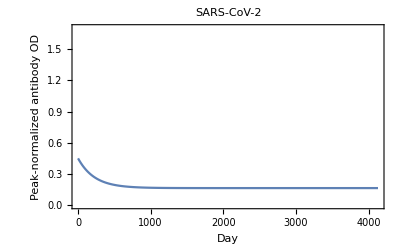

```mathematica
ListLinePlot[sarscov2antibodytimecourseB,
PlotRange->{0, 1.7},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Peak-normalized antibody OD"}]
```

This panel is part of Figure 1.

```mathematica
Export[
StringJoin["/Users/jt436/Downloads/alshukairi-gudbjartsson-SARS-CoV-2_nOD-by-Day_Pfizer_Booster", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
ListLinePlot[sarscov2antibodytimecourseB,
PlotRange->{0, 1.7},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Peak-normalized antibody OD"}]
]
```

Export::nodir: Directory /Users/jt436/Downloads/ does not exist.

Export::noopen: Cannot open /Users/jt436/Downloads/alshukairi-gudbjartsson-SARS-CoV-2_nOD-by-Day_Pfizer_Booster04May2023.pdf.

$Failed

### SARS-CoV-2 Probability of Infection | Antibody OD

```mathematica
sarscov2probinfgivenaod[aod_]:=1/(1+Exp[-(-5.841733+-5.323444*aod)])
```

These values for a and b come from the ancestral and descendent states natural infection analysis to determine them for the zoonotic coronaviruses given baselines and declines for all viruses, and a’s and b’s for the “seasonal” coronaviruses. See Townsend et al. 2021 “The durability of immunity against reinfection by SARS-CoV-2: a comparative evolutionary study”, The Lancet Microbe.

```mathematica
sarscov2probinfgivenaod[aod]
```

1/(1+ⅇ^(5.84173+5.32344 aod))

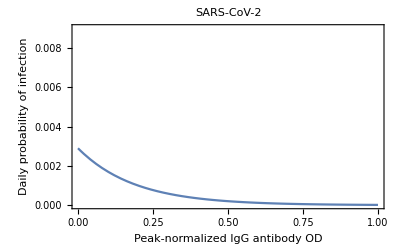

```mathematica
Plot[sarscov2probinfgivenaod[x],{x,0,1},
 PlotRange->{0,0.009},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Peak-normalized IgG antibody OD", "Daily probability of infection"}
]
```

This panel is part of Figure 1.

```mathematica
Export[
StringJoin["/Users/jt436/Downloads/alshukairi-gudbjartsson-SARS-CoV-2_PrInf-by-nOD_Pfizer_Booster", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
Plot[sarscov2probinfgivenaod[x],{x,0,1},
 PlotRange->{0,0.009},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Peak-normalized IgG antibody OD", "Daily probability of infection"}
]
]
```

Export::nodir: Directory /Users/jt436/Downloads/ does not exist.

Export::noopen: Cannot open /Users/jt436/Downloads/alshukairi-gudbjartsson-SARS-CoV-2_PrInf-by-nOD_Pfizer_Booster04May2023.pdf.

$Failed

```mathematica
sarscov2probinfgivenall[a_, b_, aod_]:=1/(1+Exp[-(a+b*aod)])
```

### SARS-CoV-2 Probability of No Reinfection Time Course

```mathematica
sarscov2probnoreinfectiontimecourse={1};
day=1;
AppendTo[sarscov2probnoreinfectiontimecourse, 
sarscov2probnoreinfectiontimecourse[[day]]*(1-sarscov2probinfgivenaod[sarscov2antibodytimecourseB[[day+1]]])
];

While[day<4393,
Increment[day];
AppendTo[sarscov2probnoreinfectiontimecourse, 
If[day<Length[sarscov2antibodytimecourseB],
sarscov2probnoreinfectiontimecourse[[day]]*(1-sarscov2probinfgivenaod[sarscov2antibodytimecourseB[[day+1]] ]),
sarscov2probnoreinfectiontimecourse[[day]]*(1-sarscov2probinfgivenaod[sarscov2antibodytimecourseB[[1201]]])
]
]
];

sarscov2probnoreinfectiontimecourse
```

{1,0.999734,0.999465,0.999196,0.998924,0.998651,0.998375,0.998099,0.99782,0.99754,0.997258,0.996974,0.996688,0.996401,0.996112,0.995821,0.995528,0.995234,0.994938,0.99464,0.99434,0.994039,0.993735,0.99343,0.993124,0.992815,0.992505,0.992193,0.991879,0.991563,0.991246,0.990926,0.990605,0.990283,0.989958,0.989632,0.989303,0.988973,0.988642,0.988308,0.987973,0.987636,0.987297,0.986956,0.986614,0.98627,0.985924,0.985576,0.985226,0.984875,0.984521,0.984166,0.98381,0.983451,0.983091,0.982729,0.982365,0.981999,0.981631,0.981262,0.980891,0.980518,0.980143,0.979767,0.979389,0.979009,0.978627,0.978243,0.977858,0.977471,0.977082,0.976691,0.976299,0.975905,0.975509,0.975111,0.974711,0.97431,0.973907,0.973502,0.973096,0.972687,0.972277,0.971865,0.971452,0.971036,0.970619,0.9702,0.96978,0.969357,0.968933,0.968507,0.96808,0.967651,0.96722,0.966787,0.966352,0.965916,0.965478,0.965039,0.964597,0.964154,0.963709,0.963263,0.962815,0.962365,0.961913,0.96146,0.961005,0.960548,0.96009,0.95963,0.959168,0.958705,0.958239,0.957773,0.957304,0.956834,0.956362,0.955889,0.955414,0.954937,0.954459,0.953979,0.953497,0.953014,0.952529,0.952043,0.951555,0.951065,0.950573,0.950081,0.949586,0.94909,0.948592,0.948093,0.947592,0.947089,0.946585,0.946079,0.945572,0.945063,0.944553,0.944041,0.943527,0.943012,0.942495,0.941977,0.941458,0.940936,0.940413,0.939889,0.939363,0.938836,0.938307,0.937777,0.937245,0.936712,0.936177,0.935641,0.935103,0.934563,0.934023,0.933481,0.932937,0.932392,0.931845,0.931297,0.930748,0.930197,0.929645,0.929091,0.928536,0.927979,0.927421,0.926862,0.926301,0.925739,0.925175,0.92461,0.924044,0.923476,0.922907,0.922337,0.921765,0.921192,0.920617,0.920041,0.919464,0.918886,0.918306,0.917725,0.917142,0.916559,0.915974,0.915387,0.9148,0.914211,0.913621,0.913029,0.912437,0.911843,0.911247,0.910651,0.910053,0.909454,0.908854,0.908253,0.90765,0.907046,0.906441,0.905835,0.905227,0.904619,0.904009,0.903398,0.902786,0.902172,0.901558,0.900942,0.900325,0.899708,0.899088,0.898468,0.897847,0.897224,0.896601,0.895976,0.89535,0.894724,0.894096,0.893466,0.892836,0.892205,0.891573,0.89094,0.890305,0.88967,0.889033,0.888396,0.887757,0.887118,0.886477,0.885836,0.885193,0.884549,0.883905,0.883259,0.882613,0.881965,0.881317,0.880667,0.880017,0.879366,0.878713,0.87806,0.877406,0.876751,0.876095,0.875438,0.87478,0.874121,0.873462,0.872801,0.87214,0.871477,0.870814,0.87015,0.869485,0.86882,0.868153,0.867486,0.866817,0.866148,0.865478,0.864808,0.864136,0.863464,0.862791,0.862117,0.861442,0.860766,0.86009,0.859413,0.858735,0.858057,0.857377,0.856697,0.856016,0.855335,0.854653,0.85397,0.853286,0.852601,0.851916,0.851231,0.850544,0.849857,0.849169,0.84848,0.847791,0.847101,0.846411,0.845719,0.845028,0.844335,0.843642,0.842948,0.842254,0.841559,0.840863,0.840167,0.83947,0.838773,0.838075,0.837376,0.836677,0.835977,0.835277,0.834576,0.833875,0.833173,0.83247,0.831767,0.831064,0.83036,0.829655,0.82895,0.828244,0.827538,0.826831,0.826124,0.825417,0.824708,0.824,0.823291,0.822581,0.821871,0.821161,0.82045,0.819739,0.819027,0.818314,0.817602,0.816889,0.816175,0.815461,0.814747,0.814032,0.813317,0.812602,0.811886,0.81117,0.810453,0.809736,0.809019,0.808301,0.807583,0.806864,0.806145,0.805426,0.804707,0.803987,0.803267,0.802546,0.801826,0.801105,0.800383,0.799662,0.79894,0.798217,0.797495,0.796772,0.796049,0.795325,0.794602,0.793878,0.793154,0.792429,0.791705,0.79098,0.790255,0.789529,0.788804,0.788078,0.787352,0.786626,0.785899,0.785173,0.784446,0.783719,0.782991,0.782264,0.781536,0.780809,0.780081,0.779353,0.778624,0.777896,0.777167,0.776439,0.77571,0.774981,0.774252,0.773522,0.772793,0.772063,0.771334,0.770604,0.769874,0.769144,0.768414,0.767684,0.766953,0.766223,0.765493,0.764762,0.764031,0.763301,0.76257,0.761839,0.761108,0.760377,0.759647,0.758916,0.758184,0.757453,0.756722,0.755991,0.75526,0.754529,0.753797,0.753066,0.752335,0.751604,0.750872,0.750141,0.74941,0.748679,0.747947,0.747216,0.746485,0.745754,0.745023,0.744292,0.74356,0.742829,0.742098,0.741367,0.740637,0.739906,0.739175,0.738444,0.737714,0.736983,0.736252,0.735522,0.734792,0.734061,0.733331,0.732601,0.731871,0.731141,0.730411,0.729681,0.728952,0.728222,0.727493,0.726764,0.726034,0.725305,0.724576,0.723848,0.723119,0.72239,0.721662,0.720934,0.720206,0.719478,0.71875,0.718022,0.717295,0.716568,0.71584,0.715113,0.714387,0.71366,0.712934,0.712207,0.711481,0.710755,0.710029,0.709304,0.708579,0.707853,0.707129,0.706404,0.705679,0.704955,0.704231,0.703507,0.702783,0.70206,0.701337,0.700614,0.699891,0.699168,0.698446,0.697724,0.697002,0.69628,0.695559,0.694838,0.694117,0.693397,0.692676,0.691956,0.691236,0.690517,0.689797,0.689078,0.68836,0.687641,0.686923,0.686205,0.685487,0.68477,0.684053,0.683336,0.68262,0.681904,0.681188,0.680472,0.679757,0.679042,0.678327,0.677613,0.676899,0.676185,0.675471,0.674758,0.674045,0.673333,0.672621,0.671909,0.671197,0.670486,0.669775,0.669065,0.668355,0.667645,0.666935,0.666226,0.665517,0.664809,0.664101,0.663393,0.662686,0.661979,0.661272,0.660566,0.65986,0.659154,0.658449,0.657744,0.657039,0.656335,0.655631,0.654928,0.654225,0.653522,0.65282,0.652118,0.651417,0.650716,0.650015,0.649315,0.648615,0.647915,0.647216,0.646517,0.645819,0.645121,0.644423,0.643726,0.64303,0.642333,0.641637,0.640942,0.640247,0.639552,0.638858,0.638164,0.637471,0.636778,0.636085,0.635393,0.634701,0.63401,0.633319,0.632628,0.631938,0.631249,0.63056,0.629871,0.629183,0.628495,0.627807,0.627121,0.626434,0.625748,0.625062,0.624377,0.623692,0.623008,0.622324,0.621641,0.620958,0.620276,0.619594,0.618912,0.618231,0.61755,0.61687,0.61619,0.615511,0.614832,0.614154,0.613476,0.612799,0.612122,0.611446,0.61077,0.610094,0.609419,0.608745,0.608071,0.607397,0.606724,0.606051,0.605379,0.604708,0.604037,0.603366,0.602696,0.602026,0.601357,0.600688,0.60002,0.599352,0.598685,0.598018,0.597352,0.596686,0.596021,0.595356,0.594692,0.594028,0.593365,0.592702,0.59204,0.591378,0.590717,0.590056,0.589396,0.588736,0.588077,0.587418,0.58676,0.586103,0.585445,0.584789,0.584133,0.583477,0.582822,0.582167,0.581513,0.58086,0.580207,0.579554,0.578902,0.578251,0.5776,0.576949,0.576299,0.57565,0.575001,0.574353,0.573705,0.573058,0.572411,0.571765,0.571119,0.570474,0.569829,0.569185,0.568542,0.567899,0.567256,0.566614,0.565973,0.565332,0.564691,0.564052,0.563412,0.562774,0.562135,0.561498,0.56086,0.560224,0.559588,0.558952,0.558317,0.557683,0.557049,0.556416,0.555783,0.555151,0.554519,0.553888,0.553257,0.552627,0.551997,0.551369,0.55074,0.550112,0.549485,0.548858,0.548232,0.547606,0.546981,0.546356,0.545732,0.545109,0.544486,0.543864,0.543242,0.54262,0.542,0.54138,0.54076,0.540141,0.539522,0.538904,0.538287,0.53767,0.537054,0.536438,0.535823,0.535208,0.534594,0.533981,0.533368,0.532756,0.532144,0.531532,0.530922,0.530312,0.529702,0.529093,0.528485,0.527877,0.527269,0.526663,0.526056,0.525451,0.524846,0.524241,0.523637,0.523034,0.522431,0.521829,0.521227,0.520626,0.520025,0.519425,0.518826,0.518227,0.517629,0.517031,0.516434,0.515837,0.515241,0.514645,0.51405,0.513456,0.512862,0.512269,0.511676,0.511084,0.510493,0.509902,0.509311,0.508722,0.508132,0.507544,0.506955,0.506368,0.505781,0.505194,0.504609,0.504023,0.503439,0.502854,0.502271,0.501688,0.501105,0.500523,0.499942,0.499361,0.498781,0.498202,0.497623,0.497044,0.496466,0.495889,0.495312,0.494736,0.49416,0.493585,0.493011,0.492437,0.491863,0.491291,0.490718,0.490147,0.489576,0.489005,0.488435,0.487866,0.487297,0.486729,0.486161,0.485594,0.485027,0.484461,0.483896,0.483331,0.482767,0.482203,0.48164,0.481077,0.480515,0.479954,0.479393,0.478833,0.478273,0.477714,0.477155,0.476597,0.47604,0.475483,0.474927,0.474371,0.473816,0.473261,0.472707,0.472154,0.471601,0.471048,0.470496,0.469945,0.469395,0.468844,0.468295,0.467746,0.467198,0.46665,0.466102,0.465556,0.46501,0.464464,0.463919,0.463375,0.462831,0.462287,0.461745,0.461202,0.460661,0.46012,0.459579,0.459039,0.4585,0.457961,0.457423,0.456885,0.456348,0.455811,0.455275,0.45474,0.454205,0.453671,0.453137,0.452604,0.452071,0.451539,0.451008,0.450477,0.449946,0.449416,0.448887,0.448358,0.44783,0.447303,0.446775,0.446249,0.445723,0.445198,0.444673,0.444149,0.443625,0.443102,0.442579,0.442057,0.441536,0.441015,0.440494,0.439974,0.439455,0.438937,0.438418,0.437901,0.437384,0.436867,0.436351,0.435836,0.435321,0.434807,0.434293,0.43378,0.433267,0.432755,0.432244,0.431733,0.431222,0.430712,0.430203,0.429694,0.429186,0.428678,0.428171,0.427665,0.427159,0.426653,0.426148,0.425644,0.42514,0.424637,0.424134,0.423632,0.42313,0.422629,0.422128,0.421628,0.421129,0.42063,0.420131,0.419633,0.419136,0.418639,0.418143,0.417647,0.417152,0.416658,0.416164,0.41567,0.415177,0.414685,0.414193,0.413701,0.413211,0.41272,0.412231,0.411741,0.411253,0.410765,0.410277,0.40979,0.409303,0.408817,0.408332,0.407847,0.407363,0.406879,0.406395,0.405913,0.40543,0.404949,0.404467,0.403987,0.403507,0.403027,0.402548,0.40207,0.401592,0.401114,0.400637,0.400161,0.399685,0.399209,0.398735,0.39826,0.397787,0.397313,0.396841,0.396368,0.395897,0.395426,0.394955,0.394485,0.394015,0.393546,0.393078,0.39261,0.392142,0.391675,0.391209,0.390743,0.390278,0.389813,0.389348,0.388885,0.388421,0.387958,0.387496,0.387034,0.386573,0.386113,0.385652,0.385193,0.384733,0.384275,0.383817,0.383359,0.382902,0.382445,0.381989,0.381534,0.381079,0.380624,0.38017,0.379717,0.379264,0.378811,0.378359,0.377908,0.377457,0.377006,0.376556,0.376107,0.375658,0.37521,0.374762,0.374314,0.373867,0.373421,0.372975,0.37253,0.372085,0.37164,0.371197,0.370753,0.37031,0.369868,0.369426,0.368985,0.368544,0.368104,0.367664,0.367224,0.366786,0.366347,0.365909,0.365472,0.365035,0.364599,0.364163,0.363728,0.363293,0.362858,0.362424,0.361991,0.361558,0.361126,0.360694,0.360263,0.359832,0.359401,0.358971,0.358542,0.358113,0.357684,0.357256,0.356829,0.356402,0.355976,0.35555,0.355124,0.354699,0.354274,0.35385,0.353427,0.353004,0.352581,0.352159,0.351737,0.351316,0.350896,0.350475,0.350056,0.349637,0.349218,0.3488,0.348382,0.347964,0.347548,0.347131,0.346716,0.3463,0.345885,0.345471,0.345057,0.344643,0.34423,0.343818,0.343406,0.342994,0.342583,0.342173,0.341763,0.341353,0.340944,0.340535,0.340127,0.339719,0.339312,0.338905,0.338499,0.338093,0.337687,0.337282,0.336878,0.336474,0.33607,0.335667,0.335265,0.334862,0.334461,0.33406,0.333659,0.333259,0.332859,0.332459,0.33206,0.331662,0.331264,0.330867,0.33047,0.330073,0.329677,0.329281,0.328886,0.328491,0.328097,0.327703,0.32731,0.326917,0.326524,0.326132,0.325741,0.32535,0.324959,0.324569,0.324179,0.32379,0.323401,0.323013,0.322625,0.322238,0.321851,0.321464,0.321078,0.320692,0.320307,0.319922,0.319538,0.319154,0.318771,0.318388,0.318005,0.317623,0.317242,0.31686,0.31648,0.316099,0.31572,0.31534,0.314961,0.314583,0.314205,0.313827,0.31345,0.313073,0.312697,0.312321,0.311946,0.311571,0.311196,0.310822,0.310448,0.310075,0.309702,0.30933,0.308958,0.308587,0.308216,0.307845,0.307475,0.307105,0.306736,0.306367,0.305998,0.30563,0.305263,0.304896,0.304529,0.304163,0.303797,0.303431,0.303066,0.302702,0.302338,0.301974,0.301611,0.301248,0.300885,0.300523,0.300162,0.299801,0.29944,0.29908,0.29872,0.29836,0.298001,0.297643,0.297285,0.296927,0.296569,0.296213,0.295856,0.2955,0.295144,0.294789,0.294434,0.29408,0.293726,0.293372,0.293019,0.292666,0.292314,0.291962,0.291611,0.29126,0.290909,0.290559,0.290209,0.289859,0.28951,0.289162,0.288814,0.288466,0.288118,0.287772,0.287425,0.287079,0.286733,0.286388,0.286043,0.285698,0.285354,0.285011,0.284667,0.284324,0.283982,0.28364,0.283298,0.282957,0.282616,0.282276,0.281936,0.281596,0.281257,0.280918,0.280579,0.280241,0.279904,0.279567,0.27923,0.278893,0.278557,0.278222,0.277886,0.277551,0.277217,0.276883,0.276549,0.276216,0.275883,0.275551,0.275219,0.274887,0.274556,0.274225,0.273894,0.273564,0.273234,0.272905,0.272576,0.272247,0.271919,0.271591,0.271264,0.270937,0.27061,0.270284,0.269958,0.269633,0.269308,0.268983,0.268659,0.268335,0.268012,0.267688,0.267366,0.267043,0.266721,0.2664,0.266078,0.265758,0.265437,0.265117,0.264797,0.264478,0.264159,0.263841,0.263522,0.263205,0.262887,0.26257,0.262253,0.261937,0.261621,0.261306,0.26099,0.260676,0.260361,0.260047,0.259734,0.25942,0.259107,0.258795,0.258483,0.258171,0.257859,0.257548,0.257238,0.256927,0.256617,0.256308,0.255999,0.25569,0.255381,0.255073,0.254765,0.254458,0.254151,0.253844,0.253538,0.253232,0.252927,0.252621,0.252317,0.252012,0.251708,0.251404,0.251101,0.250798,0.250495,0.250193,0.249891,0.249589,0.249288,0.248987,0.248687,0.248387,0.248087,0.247788,0.247489,0.24719,0.246892,0.246594,0.246296,0.245999,0.245702,0.245405,0.245109,0.244813,0.244518,0.244222,0.243928,0.243633,0.243339,0.243045,0.242752,0.242459,0.242166,0.241874,0.241582,0.24129,0.240999,0.240708,0.240417,0.240127,0.239837,0.239548,0.239258,0.23897,0.238681,0.238393,0.238105,0.237818,0.23753,0.237244,0.236957,0.236671,0.236385,0.2361,0.235815,0.23553,0.235246,0.234962,0.234678,0.234394,0.234111,0.233829,0.233546,0.233264,0.232983,0.232701,0.23242,0.232139,0.231859,0.231579,0.231299,0.23102,0.230741,0.230462,0.230184,0.229906,0.229628,0.229351,0.229074,0.228797,0.228521,0.228245,0.227969,0.227694,0.227419,0.227144,0.22687,0.226596,0.226322,0.226049,0.225776,0.225503,0.225231,0.224958,0.224687,0.224415,0.224144,0.223873,0.223603,0.223333,0.223063,0.222794,0.222524,0.222256,0.221987,0.221719,0.221451,0.221183,0.220916,0.220649,0.220383,0.220117,0.219851,0.219585,0.21932,0.219055,0.21879,0.218526,0.218262,0.217998,0.217734,0.217471,0.217209,0.216946,0.216684,0.216422,0.216161,0.2159,0.215639,0.215378,0.215118,0.214858,0.214598,0.214339,0.21408,0.213821,0.213563,0.213305,0.213047,0.21279,0.212532,0.212276,0.212019,0.211763,0.211507,0.211251,0.210996,0.210741,0.210486,0.210232,0.209978,0.209724,0.209471,0.209217,0.208965,0.208712,0.20846,0.208208,0.207956,0.207705,0.207454,0.207203,0.206953,0.206702,0.206453,0.206203,0.205954,0.205705,0.205456,0.205208,0.20496,0.204712,0.204465,0.204218,0.203971,0.203724,0.203478,0.203232,0.202986,0.202741,0.202496,0.202251,0.202007,0.201762,0.201519,0.201275,0.201032,0.200789,0.200546,0.200303,0.200061,0.199819,0.199578,0.199337,0.199096,0.198855,0.198615,0.198374,0.198135,0.197895,0.197656,0.197417,0.197178,0.19694,0.196702,0.196464,0.196226,0.195989,0.195752,0.195516,0.195279,0.195043,0.194807,0.194572,0.194337,0.194102,0.193867,0.193632,0.193398,0.193165,0.192931,0.192698,0.192465,0.192232,0.192,0.191767,0.191536,0.191304,0.191073,0.190842,0.190611,0.19038,0.19015,0.18992,0.189691,0.189461,0.189232,0.189003,0.188775,0.188547,0.188319,0.188091,0.187863,0.187636,0.187409,0.187183,0.186956,0.18673,0.186504,0.186279,0.186054,0.185829,0.185604,0.18538,0.185155,0.184931,0.184708,0.184484,0.184261,0.184039,0.183816,0.183594,0.183372,0.18315,0.182928,0.182707,0.182486,0.182266,0.182045,0.181825,0.181605,0.181385,0.181166,0.180947,0.180728,0.18051,0.180291,0.180073,0.179855,0.179638,0.179421,0.179204,0.178987,0.17877,0.178554,0.178338,0.178123,0.177907,0.177692,0.177477,0.177262,0.177048,0.176834,0.17662,0.176406,0.176193,0.17598,0.175767,0.175554,0.175342,0.17513,0.174918,0.174707,0.174495,0.174284,0.174074,0.173863,0.173653,0.173443,0.173233,0.173023,0.172814,0.172605,0.172396,0.172188,0.171979,0.171771,0.171564,0.171356,0.171149,0.170942,0.170735,0.170529,0.170322,0.170116,0.16991,0.169705,0.1695,0.169295,0.16909,0.168885,0.168681,0.168477,0.168273,0.16807,0.167866,0.167663,0.16746,0.167258,0.167055,0.166853,0.166652,0.16645,0.166249,0.166048,0.165847,0.165646,0.165446,0.165245,0.165046,0.164846,0.164647,0.164447,0.164248,0.16405,0.163851,0.163653,0.163455,0.163257,0.16306,0.162863,0.162666,0.162469,0.162272,0.162076,0.16188,0.161684,0.161488,0.161293,0.161098,0.160903,0.160708,0.160514,0.16032,0.160126,0.159932,0.159739,0.159545,0.159352,0.159159,0.158967,0.158775,0.158583,0.158391,0.158199,0.158008,0.157816,0.157626,0.157435,0.157244,0.157054,0.156864,0.156674,0.156485,0.156295,0.156106,0.155918,0.155729,0.15554,0.155352,0.155164,0.154977,0.154789,0.154602,0.154415,0.154228,0.154041,0.153855,0.153669,0.153483,0.153297,0.153112,0.152926,0.152741,0.152557,0.152372,0.152188,0.152004,0.15182,0.151636,0.151452,0.151269,0.151086,0.150903,0.150721,0.150538,0.150356,0.150174,0.149993,0.149811,0.14963,0.149449,0.149268,0.149087,0.148907,0.148727,0.148547,0.148367,0.148188,0.148008,0.147829,0.14765,0.147472,0.147293,0.147115,0.146937,0.146759,0.146582,0.146404,0.146227,0.14605,0.145874,0.145697,0.145521,0.145345,0.145169,0.144993,0.144818,0.144642,0.144467,0.144293,0.144118,0.143944,0.143769,0.143595,0.143422,0.143248,0.143075,0.142902,0.142729,0.142556,0.142384,0.142211,0.142039,0.141867,0.141696,0.141524,0.141353,0.141182,0.141011,0.14084,0.14067,0.1405,0.14033,0.14016,0.13999,0.139821,0.139652,0.139483,0.139314,0.139145,0.138977,0.138809,0.138641,0.138473,0.138306,0.138138,0.137971,0.137804,0.137637,0.137471,0.137304,0.137138,0.136972,0.136806,0.136641,0.136476,0.13631,0.136145,0.135981,0.135816,0.135652,0.135488,0.135324,0.13516,0.134996,0.134833,0.13467,0.134507,0.134344,0.134182,0.134019,0.133857,0.133695,0.133533,0.133372,0.13321,0.133049,0.132888,0.132727,0.132567,0.132406,0.132246,0.132086,0.131926,0.131766,0.131607,0.131448,0.131289,0.13113,0.130971,0.130812,0.130654,0.130496,0.130338,0.13018,0.130023,0.129865,0.129708,0.129551,0.129395,0.129238,0.129082,0.128925,0.128769,0.128614,0.128458,0.128302,0.128147,0.127992,0.127837,0.127682,0.127528,0.127374,0.127219,0.127065,0.126912,0.126758,0.126605,0.126451,0.126298,0.126146,0.125993,0.12584,0.125688,0.125536,0.125384,0.125232,0.125081,0.124929,0.124778,0.124627,0.124476,0.124326,0.124175,0.124025,0.123875,0.123725,0.123575,0.123426,0.123276,0.123127,0.122978,0.122829,0.122681,0.122532,0.122384,0.122236,0.122088,0.12194,0.121792,0.121645,0.121498,0.121351,0.121204,0.121057,0.120911,0.120764,0.120618,0.120472,0.120326,0.120181,0.120035,0.11989,0.119745,0.1196,0.119455,0.119311,0.119166,0.119022,0.118878,0.118734,0.11859,0.118447,0.118304,0.11816,0.118017,0.117875,0.117732,0.117589,0.117447,0.117305,0.117163,0.117021,0.11688,0.116738,0.116597,0.116456,0.116315,0.116174,0.116033,0.115893,0.115753,0.115613,0.115473,0.115333,0.115193,0.115054,0.114915,0.114776,0.114637,0.114498,0.114359,0.114221,0.114083,0.113945,0.113807,0.113669,0.113531,0.113394,0.113257,0.11312,0.112983,0.112846,0.112709,0.112573,0.112437,0.112301,0.112165,0.112029,0.111893,0.111758,0.111623,0.111488,0.111353,0.111218,0.111083,0.110949,0.110814,0.11068,0.110546,0.110413,0.110279,0.110146,0.110012,0.109879,0.109746,0.109613,0.109481,0.109348,0.109216,0.109083,0.108951,0.10882,0.108688,0.108556,0.108425,0.108294,0.108163,0.108032,0.107901,0.10777,0.10764,0.10751,0.10738,0.10725,0.10712,0.10699,0.106861,0.106731,0.106602,0.106473,0.106344,0.106215,0.106087,0.105958,0.10583,0.105702,0.105574,0.105446,0.105319,0.105191,0.105064,0.104937,0.10481,0.104683,0.104556,0.10443,0.104303,0.104177,0.104051,0.103925,0.103799,0.103674,0.103548,0.103423,0.103298,0.103173,0.103048,0.102923,0.102798,0.102674,0.10255,0.102426,0.102302,0.102178,0.102054,0.101931,0.101807,0.101684,0.101561,0.101438,0.101315,0.101193,0.10107,0.100948,0.100826,0.100703,0.100582,0.10046,0.100338,0.100217,0.100096,0.0999744,0.0998534,0.0997325,0.0996118,0.0994912,0.0993708,0.0992505,0.0991304,0.0990104,0.0988905,0.0987708,0.0986513,0.0985319,0.0984126,0.0982935,0.0981745,0.0980557,0.097937,0.0978185,0.0977001,0.0975818,0.0974637,0.0973457,0.0972279,0.0971102,0.0969927,0.0968753,0.096758,0.0966409,0.0965239,0.0964071,0.0962904,0.0961738,0.0960574,0.0959412,0.095825,0.095709,0.0955932,0.0954775,0.0953619,0.0952465,0.0951312,0.095016,0.094901,0.0947862,0.0946714,0.0945568,0.0944424,0.0943281,0.0942139,0.0940999,0.093986,0.0938722,0.0937586,0.0936451,0.0935317,0.0934185,0.0933054,0.0931925,0.0930797,0.092967,0.0928545,0.0927421,0.0926299,0.0925177,0.0924057,0.0922939,0.0921822,0.0920706,0.0919592,0.0918478,0.0917367,0.0916256,0.0915147,0.0914039,0.0912933,0.0911828,0.0910724,0.0909622,0.0908521,0.0907421,0.0906323,0.0905226,0.090413,0.0903036,0.0901943,0.0900851,0.089976,0.0898671,0.0897584,0.0896497,0.0895412,0.0894328,0.0893246,0.0892164,0.0891084,0.0890006,0.0888928,0.0887852,0.0886778,0.0885704,0.0884632,0.0883561,0.0882492,0.0881424,0.0880357,0.0879291,0.0878227,0.0877164,0.0876102,0.0875042,0.0873982,0.0872925,0.0871868,0.0870813,0.0869758,0.0868706,0.0867654,0.0866604,0.0865555,0.0864507,0.0863461,0.0862416,0.0861372,0.0860329,0.0859288,0.0858247,0.0857209,0.0856171,0.0855135,0.08541,0.0853066,0.0852033,0.0851002,0.0849972,0.0848943,0.0847915,0.0846889,0.0845864,0.084484,0.0843817,0.0842796,0.0841776,0.0840757,0.0839739,0.0838722,0.0837707,0.0836693,0.083568,0.0834669,0.0833659,0.0832649,0.0831642,0.0830635,0.0829629,0.0828625,0.0827622,0.082662,0.082562,0.082462,0.0823622,0.0822625,0.082163,0.0820635,0.0819642,0.0818649,0.0817659,0.0816669,0.081568,0.0814693,0.0813707,0.0812722,0.0811738,0.0810755,0.0809774,0.0808794,0.0807815,0.0806837,0.080586,0.0804885,0.0803911,0.0802937,0.0801965,0.0800995,0.0800025,0.0799057,0.079809,0.0797123,0.0796159,0.0795195,0.0794232,0.0793271,0.0792311,0.0791352,0.0790394,0.0789437,0.0788481,0.0787527,0.0786574,0.0785621,0.078467,0.0783721,0.0782772,0.0781824,0.0780878,0.0779933,0.0778989,0.0778046,0.0777104,0.0776163,0.0775224,0.0774285,0.0773348,0.0772412,0.0771477,0.0770543,0.076961,0.0768679,0.0767748,0.0766819,0.0765891,0.0764964,0.0764038,0.0763113,0.0762189,0.0761267,0.0760345,0.0759425,0.0758505,0.0757587,0.075667,0.0755754,0.0754839,0.0753926,0.0753013,0.0752102,0.0751191,0.0750282,0.0749374,0.0748467,0.0747561,0.0746656,0.0745752,0.0744849,0.0743948,0.0743047,0.0742148,0.0741249,0.0740352,0.0739456,0.0738561,0.0737667,0.0736774,0.0735882,0.0734991,0.0734101,0.0733213,0.0732325,0.0731439,0.0730553,0.0729669,0.0728786,0.0727904,0.0727022,0.0726142,0.0725263,0.0724386,0.0723509,0.0722633,0.0721758,0.0720884,0.0720012,0.071914,0.071827,0.07174,0.0716532,0.0715665,0.0714798,0.0713933,0.0713069,0.0712206,0.0711343,0.0710482,0.0709622,0.0708763,0.0707905,0.0707049,0.0706193,0.0705338,0.0704484,0.0703631,0.0702779,0.0701929,0.0701079,0.070023,0.0699383,0.0698536,0.0697691,0.0696846,0.0696003,0.069516,0.0694319,0.0693478,0.0692639,0.06918,0.0690963,0.0690126,0.0689291,0.0688457,0.0687623,0.0686791,0.068596,0.0685129,0.06843,0.0683471,0.0682644,0.0681818,0.0680992,0.0680168,0.0679345,0.0678522,0.0677701,0.0676881,0.0676061,0.0675243,0.0674426,0.0673609,0.0672794,0.0671979,0.0671166,0.0670354,0.0669542,0.0668732,0.0667922,0.0667114,0.0666306,0.06655,0.0664694,0.0663889,0.0663086,0.0662283,0.0661481,0.0660681,0.0659881,0.0659082,0.0658284,0.0657487,0.0656691,0.0655897,0.0655103,0.065431,0.0653518,0.0652726,0.0651936,0.0651147,0.0650359,0.0649572,0.0648785,0.0648,0.0647216,0.0646432,0.064565,0.0644868,0.0644088,0.0643308,0.0642529,0.0641751,0.0640974,0.0640199,0.0639424,0.063865,0.0637877,0.0637104,0.0636333,0.0635563,0.0634794,0.0634025,0.0633258,0.0632491,0.0631725,0.0630961,0.0630197,0.0629434,0.0628672,0.0627911,0.0627151,0.0626392,0.0625634,0.0624876,0.062412,0.0623364,0.062261,0.0621856,0.0621103,0.0620352,0.0619601,0.0618851,0.0618101,0.0617353,0.0616606,0.061586,0.0615114,0.0614369,0.0613626,0.0612883,0.0612141,0.06114,0.061066,0.0609921,0.0609182,0.0608445,0.0607708,0.0606973,0.0606238,0.0605504,0.0604771,0.0604039,0.0603308,0.0602578,0.0601848,0.060112,0.0600392,0.0599665,0.0598939,0.0598214,0.059749,0.0596767,0.0596045,0.0595323,0.0594602,0.0593883,0.0593164,0.0592446,0.0591729,0.0591012,0.0590297,0.0589582,0.0588869,0.0588156,0.0587444,0.0586733,0.0586022,0.0585313,0.0584604,0.0583897,0.058319,0.0582484,0.0581779,0.0581075,0.0580371,0.0579669,0.0578967,0.0578266,0.0577566,0.0576867,0.0576169,0.0575471,0.0574775,0.0574079,0.0573384,0.057269,0.0571997,0.0571304,0.0570613,0.0569922,0.0569232,0.0568543,0.0567855,0.0567167,0.0566481,0.0565795,0.056511,0.0564426,0.0563743,0.056306,0.0562379,0.0561698,0.0561018,0.0560339,0.0559661,0.0558983,0.0558307,0.0557631,0.0556956,0.0556282,0.0555608,0.0554936,0.0554264,0.0553593,0.0552923,0.0552253,0.0551585,0.0550917,0.055025,0.0549584,0.0548919,0.0548254,0.0547591,0.0546928,0.0546266,0.0545605,0.0544944,0.0544285,0.0543626,0.0542968,0.054231,0.0541654,0.0540998,0.0540343,0.0539689,0.0539036,0.0538383,0.0537732,0.0537081,0.0536431,0.0535781,0.0535133,0.0534485,0.0533838,0.0533192,0.0532546,0.0531902,0.0531258,0.0530615,0.0529972,0.0529331,0.052869,0.052805,0.0527411,0.0526772,0.0526135,0.0525498,0.0524862,0.0524226,0.0523592,0.0522958,0.0522325,0.0521693,0.0521061,0.052043,0.05198,0.0519171,0.0518543,0.0517915,0.0517288,0.0516662,0.0516036,0.0515412,0.0514788,0.0514165,0.0513542,0.0512921,0.05123,0.051168,0.051106,0.0510441,0.0509824,0.0509206,0.050859,0.0507974,0.0507359,0.0506745,0.0506132,0.0505519,0.0504907,0.0504296,0.0503686,0.0503076,0.0502467,0.0501859,0.0501251,0.0500644,0.0500038,0.0499433,0.0498828,0.0498225,0.0497621,0.0497019,0.0496417,0.0495817,0.0495216,0.0494617,0.0494018,0.049342,0.0492823,0.0492226,0.049163,0.0491035,0.0490441,0.0489847,0.0489254,0.0488662,0.048807,0.048748,0.048689,0.04863,0.0485711,0.0485123,0.0484536,0.048395,0.0483364,0.0482779,0.0482194,0.0481611,0.0481028,0.0480445,0.0479864,0.0479283,0.0478703,0.0478123,0.0477544,0.0476966,0.0476389,0.0475812,0.0475236,0.0474661,0.0474086,0.0473513,0.0472939,0.0472367,0.0471795,0.0471224,0.0470654,0.0470084,0.0469515,0.0468946,0.0468379,0.0467812,0.0467245,0.046668,0.0466115,0.0465551,0.0464987,0.0464424,0.0463862,0.0463301,0.046274,0.046218,0.046162,0.0461061,0.0460503,0.0459946,0.0459389,0.0458833,0.0458277,0.0457723,0.0457169,0.0456615,0.0456062,0.045551,0.0454959,0.0454408,0.0453858,0.0453309,0.045276,0.0452212,0.0451664,0.0451118,0.0450572,0.0450026,0.0449481,0.0448937,0.0448394,0.0447851,0.0447309,0.0446767,0.0446227,0.0445687,0.0445147,0.0444608,0.044407,0.0443532,0.0442995,0.0442459,0.0441924,0.0441389,0.0440854,0.0440321,0.0439788,0.0439255,0.0438724,0.0438192,0.0437662,0.0437132,0.0436603,0.0436075,0.0435547,0.0435019,0.0434493,0.0433967,0.0433442,0.0432917,0.0432393,0.0431869,0.0431347,0.0430824,0.0430303,0.0429782,0.0429262,0.0428742,0.0428223,0.0427705,0.0427187,0.042667,0.0426153,0.0425638,0.0425122,0.0424608,0.0424094,0.042358,0.0423068,0.0422555,0.0422044,0.0421533,0.0421023,0.0420513,0.0420004,0.0419496,0.0418988,0.0418481,0.0417974,0.0417468,0.0416963,0.0416458,0.0415954,0.041545,0.0414947,0.0414445,0.0413943,0.0413442,0.0412942,0.0412442,0.0411943,0.0411444,0.0410946,0.0410449,0.0409952,0.0409455,0.040896,0.0408465,0.040797,0.0407476,0.0406983,0.040649,0.0405998,0.0405507,0.0405016,0.0404526,0.0404036,0.0403547,0.0403058,0.0402571,0.0402083,0.0401597,0.040111,0.0400625,0.040014,0.0399655,0.0399172,0.0398688,0.0398206,0.0397724,0.0397242,0.0396762,0.0396281,0.0395802,0.0395322,0.0394844,0.0394366,0.0393888,0.0393412,0.0392935,0.039246,0.0391985,0.039151,0.0391036,0.0390563,0.039009,0.0389618,0.0389146,0.0388675,0.0388205,0.0387735,0.0387265,0.0386797,0.0386328,0.0385861,0.0385394,0.0384927,0.0384461,0.0383996,0.0383531,0.0383067,0.0382603,0.038214,0.0381677,0.0381215,0.0380754,0.0380293,0.0379832,0.0379373,0.0378913,0.0378455,0.0377997,0.0377539,0.0377082,0.0376626,0.037617,0.0375714,0.0375259,0.0374805,0.0374351,0.0373898,0.0373446,0.0372994,0.0372542,0.0372091,0.0371641,0.0371191,0.0370741,0.0370293,0.0369844,0.0369397,0.036895,0.0368503,0.0368057,0.0367611,0.0367166,0.0366722,0.0366278,0.0365835,0.0365392,0.0364949,0.0364508,0.0364066,0.0363626,0.0363185,0.0362746,0.0362307,0.0361868,0.036143,0.0360993,0.0360556,0.0360119,0.0359683,0.0359248,0.0358813,0.0358379,0.0357945,0.0357511,0.0357079,0.0356646,0.0356215,0.0355783,0.0355353,0.0354923,0.0354493,0.0354064,0.0353635,0.0353207,0.035278,0.0352353,0.0351926,0.03515,0.0351075,0.035065,0.0350225,0.0349801,0.0349378,0.0348955,0.0348532,0.034811,0.0347689,0.0347268,0.0346848,0.0346428,0.0346009,0.034559,0.0345171,0.0344753,0.0344336,0.0343919,0.0343503,0.0343087,0.0342672,0.0342257,0.0341843,0.0341429,0.0341016,0.0340603,0.0340191,0.0339779,0.0339367,0.0338957,0.0338546,0.0338136,0.0337727,0.0337318,0.033691,0.0336502,0.0336095,0.0335688,0.0335282,0.0334876,0.033447,0.0334065,0.0333661,0.0333257,0.0332854,0.0332451,0.0332048,0.0331646,0.0331245,0.0330844,0.0330443,0.0330043,0.0329644,0.0329245,0.0328846,0.0328448,0.0328051,0.0327654,0.0327257,0.0326861,0.0326465,0.032607,0.0325675,0.0325281,0.0324887,0.0324494,0.0324101,0.0323709,0.0323317,0.0322926,0.0322535,0.0322144,0.0321754,0.0321365,0.0320976,0.0320587,0.0320199,0.0319811,0.0319424,0.0319038,0.0318651,0.0318266,0.031788,0.0317496,0.0317111,0.0316727,0.0316344,0.0315961,0.0315579,0.0315197,0.0314815,0.0314434,0.0314053,0.0313673,0.0313293,0.0312914,0.0312535,0.0312157,0.0311779,0.0311402,0.0311025,0.0310648,0.0310272,0.0309897,0.0309522,0.0309147,0.0308773,0.0308399,0.0308026,0.0307653,0.030728,0.0306908,0.0306537,0.0306166,0.0305795,0.0305425,0.0305055,0.0304686,0.0304317,0.0303949,0.0303581,0.0303213,0.0302846,0.030248,0.0302113,0.0301748,0.0301382,0.0301018,0.0300653,0.0300289,0.0299926,0.0299563,0.02992,0.0298838,0.0298476,0.0298115,0.0297754,0.0297393,0.0297033,0.0296674,0.0296315,0.0295956,0.0295598,0.029524,0.0294883,0.0294526,0.0294169,0.0293813,0.0293457,0.0293102,0.0292747,0.0292393,0.0292039,0.0291685,0.0291332,0.029098,0.0290627,0.0290276,0.0289924,0.0289573,0.0289223,0.0288873,0.0288523,0.0288174,0.0287825,0.0287476,0.0287128,0.0286781,0.0286434,0.0286087,0.0285741,0.0285395,0.0285049,0.0284704,0.028436,0.0284015,0.0283672,0.0283328,0.0282985,0.0282643,0.02823,0.0281959,0.0281617,0.0281277,0.0280936,0.0280596,0.0280256,0.0279917,0.0279578,0.027924,0.0278902,0.0278564,0.0278227,0.027789,0.0277554,0.0277218,0.0276882,0.0276547,0.0276212,0.0275878,0.0275544,0.027521,0.0274877,0.0274544,0.0274212,0.027388,0.0273549,0.0273217,0.0272887,0.0272556,0.0272226,0.0271897,0.0271568,0.0271239,0.0270911,0.0270583,0.0270255,0.0269928,0.0269601,0.0269275,0.0268949,0.0268623,0.0268298,0.0267973,0.0267649,0.0267325,0.0267001,0.0266678,0.0266355,0.0266033,0.0265711,0.0265389,0.0265068,0.0264747,0.0264427,0.0264107,0.0263787,0.0263468,0.0263149,0.026283,0.0262512,0.0262194,0.0261877,0.026156,0.0261243,0.0260927,0.0260611,0.0260296,0.025998,0.0259666,0.0259351,0.0259037,0.0258724,0.0258411,0.0258098,0.0257785,0.0257473,0.0257162,0.025685,0.0256539,0.0256229,0.0255919,0.0255609,0.02553,0.025499,0.0254682,0.0254374,0.0254066,0.0253758,0.0253451,0.0253144,0.0252838,0.0252532,0.0252226,0.0251921,0.0251616,0.0251311,0.0251007,0.0250703,0.0250399,0.0250096,0.0249794,0.0249491,0.0249189,0.0248888,0.0248586,0.0248285,0.0247985,0.0247685,0.0247385,0.0247085,0.0246786,0.0246487,0.0246189,0.0245891,0.0245593,0.0245296,0.0244999,0.0244703,0.0244406,0.024411,0.0243815,0.024352,0.0243225,0.0242931,0.0242637,0.0242343,0.0242049,0.0241756,0.0241464,0.0241172,0.024088,0.0240588,0.0240297,0.0240006,0.0239715,0.0239425,0.0239135,0.0238846,0.0238557,0.0238268,0.0237979,0.0237691,0.0237404,0.0237116,0.0236829,0.0236543,0.0236256,0.023597,0.0235685,0.0235399,0.0235114,0.023483,0.0234545,0.0234262,0.0233978,0.0233695,0.0233412,0.0233129,0.0232847,0.0232565,0.0232284,0.0232002,0.0231722,0.0231441,0.0231161,0.0230881,0.0230602,0.0230322,0.0230044,0.0229765,0.0229487,0.0229209,0.0228932,0.0228655,0.0228378,0.0228101,0.0227825,0.022755,0.0227274,0.0226999,0.0226724,0.022645,0.0226176,0.0225902,0.0225628,0.0225355,0.0225082,0.022481,0.0224538,0.0224266,0.0223995,0.0223723,0.0223453,0.0223182,0.0222912,0.0222642,0.0222373,0.0222103,0.0221834,0.0221566,0.0221298,0.022103,0.0220762,0.0220495,0.0220228,0.0219962,0.0219695,0.0219429,0.0219164,0.0218898,0.0218633,0.0218369,0.0218104,0.021784,0.0217577,0.0217313,0.021705,0.0216787,0.0216525,0.0216263,0.0216001,0.021574,0.0215479,0.0215218,0.0214957,0.0214697,0.0214437,0.0214177,0.0213918,0.0213659,0.0213401,0.0213142,0.0212884,0.0212627,0.0212369,0.0212112,0.0211855,0.0211599,0.0211343,0.0211087,0.0210831,0.0210576,0.0210321,0.0210067,0.0209812,0.0209558,0.0209305,0.0209051,0.0208798,0.0208545,0.0208293,0.0208041,0.0207789,0.0207538,0.0207286,0.0207035,0.0206785,0.0206534,0.0206284,0.0206035,0.0205785,0.0205536,0.0205287,0.0205039,0.0204791,0.0204543,0.0204295,0.0204048,0.0203801,0.0203554,0.0203308,0.0203062,0.0202816,0.020257,0.0202325,0.020208,0.0201836,0.0201591,0.0201347,0.0201103,0.020086,0.0200617,0.0200374,0.0200131,0.0199889,0.0199647,0.0199406,0.0199164,0.0198923,0.0198682,0.0198442,0.0198202,0.0197962,0.0197722,0.0197483,0.0197244,0.0197005,0.0196766,0.0196528,0.019629,0.0196053,0.0195815,0.0195578,0.0195341,0.0195105,0.0194869,0.0194633,0.0194397,0.0194162,0.0193927,0.0193692,0.0193458,0.0193224,0.019299,0.0192756,0.0192523,0.019229,0.0192057,0.0191824,0.0191592,0.019136,0.0191129,0.0190897,0.0190666,0.0190435,0.0190205,0.0189975,0.0189745,0.0189515,0.0189285,0.0189056,0.0188828,0.0188599,0.0188371,0.0188143,0.0187915,0.0187687,0.018746,0.0187233,0.0187007,0.018678,0.0186554,0.0186328,0.0186103,0.0185877,0.0185652,0.0185428,0.0185203,0.0184979,0.0184755,0.0184531,0.0184308,0.0184085,0.0183862,0.018364,0.0183417,0.0183195,0.0182973,0.0182752,0.0182531,0.018231,0.0182089,0.0181869,0.0181649,0.0181429,0.0181209,0.018099,0.0180771,0.0180552,0.0180333,0.0180115,0.0179897,0.0179679,0.0179462,0.0179244,0.0179027,0.0178811,0.0178594,0.0178378,0.0178162,0.0177946,0.0177731,0.0177516,0.0177301,0.0177086,0.0176872,0.0176658,0.0176444,0.017623,0.0176017,0.0175804,0.0175591,0.0175379,0.0175166,0.0174954,0.0174742,0.0174531,0.017432,0.0174109,0.0173898,0.0173687,0.0173477,0.0173267,0.0173057,0.0172848,0.0172639,0.017243,0.0172221,0.0172012,0.0171804,0.0171596,0.0171389,0.0171181,0.0170974,0.0170767,0.017056,0.0170354,0.0170147,0.0169942,0.0169736,0.016953,0.0169325,0.016912,0.0168915,0.0168711,0.0168507,0.0168303,0.0168099,0.0167895,0.0167692,0.0167489,0.0167287,0.0167084,0.0166882,0.016668,0.0166478,0.0166276,0.0166075,0.0165874,0.0165673,0.0165473,0.0165272,0.0165072,0.0164873,0.0164673,0.0164474,0.0164275,0.0164076,0.0163877,0.0163679,0.0163481,0.0163283,0.0163085,0.0162888,0.016269,0.0162493,0.0162297,0.01621,0.0161904,0.0161708,0.0161512,0.0161317,0.0161122,0.0160926,0.0160732,0.0160537,0.0160343,0.0160149,0.0159955,0.0159761,0.0159568,0.0159375,0.0159182,0.0158989,0.0158797,0.0158604,0.0158412,0.0158221,0.0158029,0.0157838,0.0157647,0.0157456,0.0157265,0.0157075,0.0156885,0.0156695,0.0156505,0.0156316,0.0156126,0.0155937,0.0155749,0.015556,0.0155372,0.0155184,0.0154996,0.0154808,0.0154621,0.0154434,0.0154247,0.015406,0.0153874,0.0153687,0.0153501,0.0153315,0.015313,0.0152944,0.0152759,0.0152574,0.015239,0.0152205,0.0152021,0.0151837,0.0151653,0.015147,0.0151286,0.0151103,0.015092,0.0150737,0.0150555,0.0150373,0.0150191,0.0150009,0.0149827,0.0149646,0.0149465,0.0149284,0.0149103,0.0148923,0.0148742,0.0148562,0.0148382,0.0148203,0.0148023,0.0147844,0.0147665,0.0147487,0.0147308,0.014713,0.0146952,0.0146774,0.0146596,0.0146419,0.0146241,0.0146064,0.0145887,0.0145711,0.0145534,0.0145358,0.0145182,0.0145007,0.0144831,0.0144656,0.0144481,0.0144306,0.0144131,0.0143957,0.0143782,0.0143608,0.0143434,0.0143261,0.0143087,0.0142914,0.0142741,0.0142568,0.0142396,0.0142223,0.0142051,0.0141879,0.0141708,0.0141536,0.0141365,0.0141194,0.0141023,0.0140852,0.0140681,0.0140511,0.0140341,0.0140171,0.0140001,0.0139832,0.0139663,0.0139494,0.0139325,0.0139156,0.0138988,0.0138819,0.0138651,0.0138484,0.0138316,0.0138148,0.0137981,0.0137814,0.0137647,0.0137481,0.0137314,0.0137148,0.0136982,0.0136816,0.0136651,0.0136485,0.013632,0.0136155,0.013599,0.0135826,0.0135661,0.0135497,0.0135333,0.0135169,0.0135005,0.0134842,0.0134679,0.0134516,0.0134353,0.013419,0.0134028,0.0133866,0.0133704,0.0133542,0.013338,0.0133219,0.0133057,0.0132896,0.0132735,0.0132575,0.0132414,0.0132254,0.0132094,0.0131934,0.0131774,0.0131615,0.0131455,0.0131296,0.0131137,0.0130979,0.013082,0.0130662,0.0130503,0.0130345,0.0130188,0.013003,0.0129873,0.0129715,0.0129558,0.0129402,0.0129245,0.0129089,0.0128932,0.0128776,0.012862,0.0128465,0.0128309,0.0128154,0.0127999,0.0127844,0.0127689,0.0127534,0.012738,0.0127226,0.0127072,0.0126918,0.0126764,0.0126611,0.0126458,0.0126305,0.0126152,0.0125999,0.0125846,0.0125694,0.0125542,0.012539,0.0125238,0.0125087,0.0124935,0.0124784,0.0124633,0.0124482,0.0124331,0.0124181,0.012403,0.012388,0.012373,0.0123581,0.0123431,0.0123282,0.0123132,0.0122983,0.0122834,0.0122686,0.0122537,0.0122389,0.0122241,0.0122093,0.0121945,0.0121797,0.012165,0.0121503,0.0121355,0.0121209,0.0121062,0.0120915,0.0120769,0.0120623,0.0120477,0.0120331,0.0120185,0.012004,0.0119894,0.0119749,0.0119604,0.011946,0.0119315,0.011917,0.0119026,0.0118882,0.0118738,0.0118595,0.0118451,0.0118308,0.0118164,0.0118021,0.0117878,0.0117736,0.0117593,0.0117451,0.0117309,0.0117167,0.0117025,0.0116883,0.0116742,0.01166,0.0116459,0.0116318,0.0116177,0.0116037,0.0115896,0.0115756,0.0115616,0.0115476,0.0115336,0.0115197,0.0115057,0.0114918,0.0114779,0.011464,0.0114501,0.0114362,0.0114224,0.0114086,0.0113948,0.011381,0.0113672,0.0113534,0.0113397,0.011326,0.0113122,0.0112986,0.0112849,0.0112712,0.0112576,0.0112439,0.0112303,0.0112167,0.0112032,0.0111896,0.0111761,0.0111625,0.011149,0.0111355,0.011122,0.0111086,0.0110951,0.0110817,0.0110683,0.0110549,0.0110415,0.0110281,0.0110148,0.0110014,0.0109881,0.0109748,0.0109615,0.0109483,0.010935,0.0109218,0.0109086,0.0108954,0.0108822,0.010869,0.0108558,0.0108427,0.0108296,0.0108165,0.0108034,0.0107903,0.0107772,0.0107642,0.0107512,0.0107381,0.0107251,0.0107122,0.0106992,0.0106862,0.0106733,0.0106604,0.0106475,0.0106346,0.0106217,0.0106089,0.010596,0.0105832,0.0105704,0.0105576,0.0105448,0.010532,0.0105193,0.0105066,0.0104938,0.0104811,0.0104684,0.0104558,0.0104431,0.0104305,0.0104178,0.0104052,0.0103926,0.0103801,0.0103675,0.0103549,0.0103424,0.0103299,0.0103174,0.0103049,0.0102924,0.01028,0.0102675,0.0102551,0.0102427,0.0102303,0.0102179,0.0102055,0.0101932,0.0101808,0.0101685,0.0101562,0.0101439,0.0101316,0.0101194,0.0101071,0.0100949,0.0100827,0.0100704,0.0100583,0.0100461,0.0100339,0.0100218,0.0100096,0.00999752,0.00998542,0.00997333,0.00996126,0.0099492,0.00993716,0.00992513,0.00991311,0.00990111,0.00988913,0.00987716,0.0098652,0.00985326,0.00984133,0.00982942,0.00981752,0.00980564,0.00979377,0.00978191,0.00977007,0.00975824,0.00974643,0.00973463,0.00972285,0.00971108,0.00969932,0.00968758,0.00967585,0.00966414,0.00965244,0.00964076,0.00962909,0.00961743,0.00960579,0.00959416,0.00958255,0.00957095,0.00955936,0.00954779,0.00953623,0.00952469,0.00951316,0.00950164,0.00949014,0.00947865,0.00946718,0.00945572,0.00944427,0.00943284,0.00942142,0.00941001,0.00939862,0.00938725,0.00937588,0.00936453,0.0093532,0.00934187,0.00933057,0.00931927,0.00930799,0.00929672,0.00928547,0.00927423,0.009263,0.00925179,0.00924059,0.0092294,0.00921823,0.00920707,0.00919593,0.00918479,0.00917367,0.00916257,0.00915148,0.0091404,0.00912934,0.00911828,0.00910725,0.00909622,0.00908521,0.00907421,0.00906323,0.00905234,0.00904146,0.00903059,0.00901974,0.0090089,0.00899807,0.00898726,0.00897645,0.00896567,0.00895489,0.00894413,0.00893338,0.00892264,0.00891192,0.00890121,0.00889051,0.00887983,0.00886915,0.0088585,0.00884785,0.00883722,0.00882659,0.00881599,0.00880539,0.00879481,0.00878424,0.00877368,0.00876314,0.00875261,0.00874209,0.00873158,0.00872109,0.0087106,0.00870014,0.00868968,0.00867924,0.00866881,0.00865839,0.00864798,0.00863759,0.00862721,0.00861684,0.00860648,0.00859614,0.00858581,0.00857549,0.00856518,0.00855489,0.00854461,0.00853434,0.00852408,0.00851384,0.0085036,0.00849338,0.00848318,0.00847298,0.0084628,0.00845263,0.00844247,0.00843232,0.00842219,0.00841207,0.00840196,0.00839186,0.00838177,0.0083717,0.00836164,0.00835159,0.00834155,0.00833153,0.00832151,0.00831151,0.00830152,0.00829155,0.00828158,0.00827163,0.00826169,0.00825176,0.00824184,0.00823194,0.00822204,0.00821216,0.00820229,0.00819243,0.00818259,0.00817275,0.00816293,0.00815312,0.00814332,0.00813354,0.00812376,0.008114,0.00810425,0.00809451,0.00808478,0.00807506,0.00806536,0.00805566,0.00804598,0.00803631,0.00802665,0.00801701,0.00800737,0.00799775,0.00798814,0.00797854,0.00796895,0.00795937,0.0079498,0.00794025,0.00793071,0.00792118,0.00791166,0.00790215,0.00789265,0.00788316,0.00787369,0.00786423,0.00785478,0.00784534,0.00783591,0.00782649,0.00781708,0.00780769,0.00779831,0.00778893,0.00777957,0.00777022,0.00776088,0.00775156,0.00774224,0.00773294,0.00772364,0.00771436,0.00770509,0.00769583,0.00768658,0.00767734,0.00766811,0.0076589,0.00764969,0.0076405,0.00763132,0.00762215,0.00761299,0.00760384,0.0075947,0.00758557,0.00757645,0.00756735,0.00755825,0.00754917,0.0075401,0.00753104,0.00752198,0.00751294,0.00750391,0.0074949,0.00748589,0.00747689,0.00746791,0.00745893,0.00744997,0.00744101,0.00743207,0.00742314,0.00741422,0.00740531,0.00739641,0.00738752,0.00737864,0.00736977,0.00736091,0.00735207,0.00734323,0.00733441,0.00732559,0.00731679,0.00730799,0.00729921,0.00729044,0.00728168,0.00727292,0.00726418,0.00725545,0.00724673,0.00723802,0.00722933,0.00722064,0.00721196,0.00720329,0.00719463,0.00718599,0.00717735,0.00716873,0.00716011,0.0071515,0.00714291,0.00713433,0.00712575,0.00711719,0.00710863,0.00710009,0.00709156,0.00708303,0.00707452,0.00706602,0.00705753,0.00704905,0.00704057,0.00703211,0.00702366,0.00701522,0.00700679,0.00699837,0.00698996,0.00698156,0.00697317,0.00696478,0.00695641,0.00694805,0.0069397,0.00693136,0.00692303,0.00691471,0.0069064,0.0068981,0.00688981,0.00688153,0.00687326,0.006865,0.00685675,0.00684851,0.00684028,0.00683206,0.00682385,0.00681565,0.00680745,0.00679927,0.0067911,0.00678294,0.00677479,0.00676665,0.00675851,0.00675039,0.00674228,0.00673417,0.00672608,0.006718,0.00670992,0.00670186,0.00669381,0.00668576,0.00667773,0.0066697,0.00666168,0.00665368,0.00664568,0.00663769,0.00662972,0.00662175,0.00661379,0.00660584,0.0065979,0.00658997}

```mathematica
probnoreinf1mtimecourse=Take[sarscov2probnoreinfectiontimecourse,30];
probnoreinf1m=Part[sarscov2probnoreinfectiontimecourse, 30];
prob1movr6y=Catenate[NestList[#*probnoreinf1m&,probnoreinf1mtimecourse,71]];
prob1movr2y=Catenate[NestList[#*probnoreinf1m&,probnoreinf1mtimecourse,23]];
```

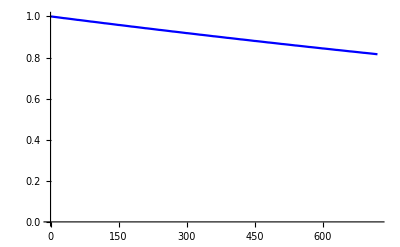

```mathematica
plot1m=ListLinePlot[prob1movr2y, PlotStyle->Blue, PlotRange->{0,1}]
```

```mathematica
probnoreinf3mtimecourse=Take[sarscov2probnoreinfectiontimecourse,90];
probnoreinf3m=Part[sarscov2probnoreinfectiontimecourse, 90];
prob3movr6y=Catenate[NestList[#*probnoreinf3m&,probnoreinf3mtimecourse,23]];
prob3movr2y=Catenate[NestList[#*probnoreinf3m&,probnoreinf3mtimecourse,7]];
```

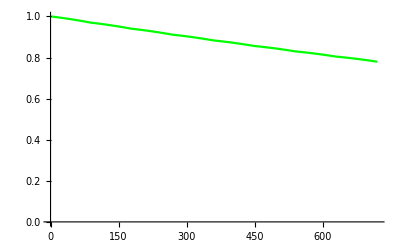

```mathematica
plot3m=ListLinePlot[prob3movr2y, PlotStyle->Green, PlotRange->{0,1}]
```

```mathematica
probnoreinf6mtimecourse=Take[sarscov2probnoreinfectiontimecourse,183];
probnoreinf6m=Part[sarscov2probnoreinfectiontimecourse, 183];
prob6movr6y=Catenate[NestList[#*probnoreinf6m&,probnoreinf6mtimecourse,11]];
prob6movr2y=Catenate[NestList[#*probnoreinf6m&,probnoreinf6mtimecourse,3]];
```

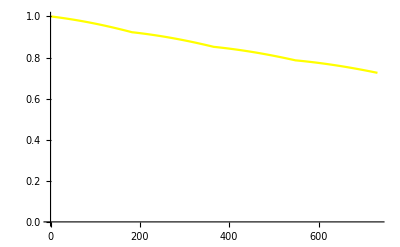

```mathematica
plot6m=ListLinePlot[prob6movr2y, PlotStyle->Yellow, PlotRange->{0,1}]
```

```mathematica
probnoreinf1ytimecourse=Take[sarscov2probnoreinfectiontimecourse,365];
probnoreinf1y=Part[sarscov2probnoreinfectiontimecourse, 365];
prob1yovr6y=Catenate[NestList[#*probnoreinf1y&,probnoreinf1ytimecourse,5]];
prob1yovr2y=Catenate[NestList[#*probnoreinf1y&,probnoreinf1ytimecourse,1]];
```

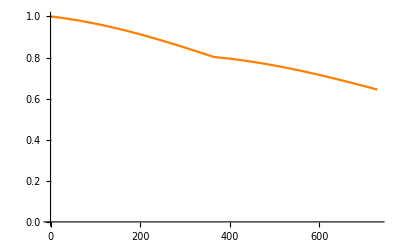

```mathematica
plot1y=ListLinePlot[prob1yovr2y, PlotStyle->Orange, PlotRange->{0,1}]
```

```mathematica
probnoreinf2ytimecourse=Take[sarscov2probnoreinfectiontimecourse,730];
probnoreinf2y=Part[sarscov2probnoreinfectiontimecourse, 730];
prob2yovr6y=Catenate[NestList[#*probnoreinf2y&,probnoreinf2ytimecourse,2]];
prob2yovr2y=Take[sarscov2probnoreinfectiontimecourse,730];
```

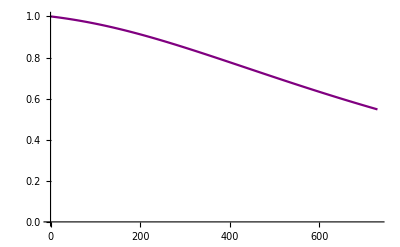

```mathematica
plot2y=ListLinePlot[prob2yovr2y, PlotStyle->Purple, PlotRange->{0,1}]
```

```mathematica
probnoreinf6ytimecourse=Take[sarscov2probnoreinfectiontimecourse,2190];
```

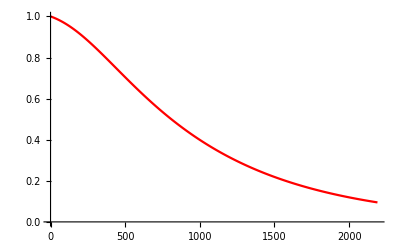

```mathematica
plot6y=ListLinePlot[probnoreinf6ytimecourse, PlotStyle->Red, PlotRange->{0,1}]
```

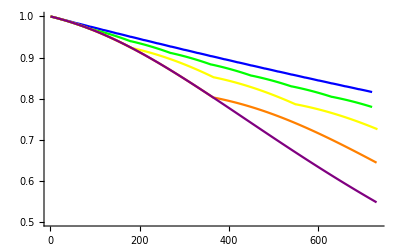

```mathematica
Show[plot1m,plot3m,plot6m,plot1y,plot2y,
PlotRange->{0.5,1}]
```

```mathematica
Export[
StringJoin["/Users/hayley/Documents/townsend/spring-23/cancer/figs/rituximab_boosterovrtime-by-Day_", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
Show[plot1m,plot3m,plot6m,plot1y,plot2y,
PlotRange->{0.5,1},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},FrameLabel->{"Day", "Probability of no reinfection"}]
]
```

/Users/hayley/Documents/townsend/spring-23/cancer/figs/rituximab_boosterovrtime-by-Day_04May2023.pdf

```mathematica
Show[1-Last[prob2yovr2y], 1-Last[prob1yovr2y], 1-Last[prob6movr2y], 1-Last[prob3movr2y],1-Last[prob1movr2y]]
```

Show::gcomb: Could not combine the graphics objects in Show[0.452394,0.355919,0.274509,0.220401,0.184005].

Show[0.452394,0.355919,0.274509,0.220401,0.184005]

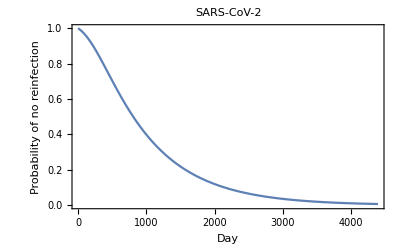

```mathematica
ListLinePlot[sarscov2probnoreinfectiontimecourse,
PlotRange->{0,1},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Probability of no reinfection"}]
```

```mathematica
Export[
StringJoin["/Users//jt436/Downloads/Pfizer_alshukairi-gudbjartsson-VoV2_PnorInfTimecourse-by-Day_", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
ListLinePlot[sarscov2probnoreinfectiontimecourse,
PlotRange->{0,1},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},FrameLabel->{"Day", "Probability of no reinfection"}]
]
```

Export::nodir: Directory /Users/jt436/Downloads/ does not exist.

Export::noopen: Cannot open /Users//jt436/Downloads/Pfizer_alshukairi-gudbjartsson-VoV2_PnorInfTimecourse-by-Day_04May2023.pdf.

$Failed

```mathematica
sarscov2continuousprobnoreinfection=Interpolation[sarscov2probnoreinfectiontimecourse]
```

InterpolatingFunction[…]

```mathematica
{x, x/30, x/365}/.
FindMinimum[{Abs[sarscov2continuousprobnoreinfection[x]-0.95],
1≤x≤4.39*10^3},
 {x, 1000}] [[2]]
```

{132.163,4.40543,0.36209}

These are the 5% quantiles for the probability of no reinfection, in days, months, and years.

```mathematica
{x, x/30, x/365}/.
FindMinimum[{Abs[sarscov2continuousprobnoreinfection[x]-0.50],
1≤x≤4.39*10^3},
 {x, 1000}] [[2]]
```

{808.9,26.9633,2.21617}

These are the 50% quantiles (medians) for the probability of no reinfection, in days, months, and years.

```mathematica
{x, x/30, x/365}/.
FindMinimum[{Abs[sarscov2continuousprobnoreinfection[x]-0.05],
1≤x≤4.39*10^3},
 {x, 1000}] [[2]]
```

{2719.06,90.6354,7.44949}

These are the 95% quantiles for the probability of no reinfection, in days, months, and years.

```mathematica
sarscov2probreinfectiondensity={};
day=0;
While[day<4393,
Increment[day];
AppendTo[sarscov2probreinfectiondensity, 
If[day<1201,
sarscov2probinfgivenaod[sarscov2antibodytimecourseB[[day]]]*sarscov2probnoreinfectiontimecourse[[day]],
sarscov2probinfgivenaod[sarscov2antibodytimecourseB[[1201]]]*sarscov2probnoreinfectiontimecourse[[day]]
]
]
];
```

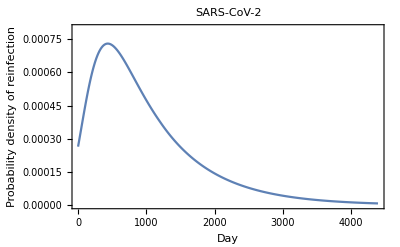

```mathematica
ListLinePlot[sarscov2probreinfectiondensity,
 PlotLabel->"SARS-CoV-2",
PlotRange->{0, 0.0008},
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Probability density of reinfection"}]
```

This panel is part of Figure 1.

```mathematica
Export[
StringJoin["/Users/jt436/Downloads/Pfizer_alshukairi-gudbjartsson-SARS-CoV-2_PrInf-by-Day_", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
ListLinePlot[sarscov2probreinfectiondensity,
 PlotLabel->"SARS-CoV-2",
PlotRange->{0, 0.0005},
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Probability density of reinfection"}]
]
```

Export::nodir: Directory /Users/jt436/Downloads/ does not exist.

Export::noopen: Cannot open /Users/jt436/Downloads/Pfizer_alshukairi-gudbjartsson-SARS-CoV-2_PrInf-by-Day_04May2023.pdf.

$Failed